## Single dot in 2D Relaxation in the absence of tunneling

```mathematica
(* Kirchhoff's equations for charges *)
```

```mathematica
M={{1/C1,1/C2,0},{1/C1,0,RG},{1,-1,0}};
b={VR-VL,ϕ-VL,n e+QG};
{Q1,Q2,IG}=LinearSolve[M,b]
```

{(C1 e n+C1 QG-C1 C2 VL+C1 C2 VR)/(C1+C2),(-C2 e n-C2 QG-C1 C2 VL+C1 C2 VR)/(C1+C2),(-e n-QG-C1 VL-C2 VR+C1 ϕ+C2 ϕ)/((C1+C2) RG)}

```mathematica
{(C1 e n+C1 QG-C1 C2 VL+C1 C2 VR)/(C1+C2),(-C2 e n-C2 QG-C1 C2 VL+C1 C2 VR)/(C1+C2),(-e n-QG-C1 VL-C2 VR+C1 ϕ+C2 ϕ)/((C1+C2) RG)}
```

{(C1 e n+C1 QG-C1 C2 VL+C1 C2 VR)/(C1+C2),(-C2 e n-C2 QG-C1 C2 VL+C1 C2 VR)/(C1+C2),(-e n-QG-C1 VL-C2 VR+C1 ϕ+C2 ϕ)/((C1+C2) RG)}

## Energy

```mathematica
Energy=Simplify[1/2(Q1^2/C1+Q2^2/C2+QG^2/CG)+Q1 VL-Q2 VR]
Work1plus = Simplify[(Energy/.n-> n+1)-Energy -e VL]
Work2plus = Simplify[(Energy/.n-> n+1)-Energy -e VR]
Work1minus = Simplify[(Energy/.n-> n-1)-Energy +e VL]
Work2minus = Simplify[(Energy/.n-> n-1)-Energy +e VR]
```

1/2 (Q1^2/C1+Q2^2/C2+QG^2/CG)+Q1 VL-Q2 VR

-e VL

-e VR

e VL

e VR

```mathematica
1/2 (Q1^2/C1+Q2^2/C2+QG^2/CG)+Q1 VL-Q2 VR
```

1/2 (Q1^2/C1+Q2^2/C2+QG^2/CG)+Q1 VL-Q2 VR

```mathematica
(e (e+2 e n+2 (QG+C2 (-VL+VR))))/(2 (C1+C2))
```

(e (e+2 e n+2 (QG+C2 (-VL+VR))))/(2 (C1+C2))

## Master Equation Solution

```mathematica
(* master equation general solution *)
pnonnorm= (R2/R1)^n Product[(α-m)/(β+m),{m,nmin,n-1}];
norm=Sum[pnonnorm,{n,nmin,nmax}];
p=pnonnorm/norm;
navg=Sum[n p,{n,nmin,nmax}];
(* Binomial Approximation *)
pbinomial = Binomial[nmax-nmin,n-nmin](R2/R1)^(n-nmin)/(1+R2/R1)^(nmax-nmin);
(* Small V approx *)
pnonnormsmallv= (R2/R1)^n Product[(α-m)/(β+m),{m,nmin,n-1}];
normsmallv=Sum[pnonnormsmallv,{n,nmin,nmin+1}];
psmallv=pnonnormsmallv/normsmallv;
navgsmallv = Sum[n psmallv,{n,nmin,nmin+1}];
(* Average current *)
pmax=p/.n-> nmax;
pmin=p/.n-> nmin;
Wmax=1/2+nmax+QG/e-(C2 V)/e;
Wmin=1/2-nmin-QG/e-(C1 V)/e;
current =Piecewise[{{ V/(R1+R2)-e/((C1+C2)(R1+R2))(1-pmax Wmax-pmin Wmin),nmax>nmin}},0];
```

Fast Relaxation

### Probability function

```mathematica
(* defining parameters *) 
αvalfast=(C2 V(C1+C2+CG))/(e(C1+C2))-CG/(e(C1+C2))((C1+C2)ϕ-C1 VL-C2 VR) - 1/2-CG/(2(C1+C2));
βvalfast=(C1 V(C1+C2+CG))/(e(C1+C2))+CG/(e(C1+C2))((C1+C2)ϕ-C1 VL-C2 VR) + 1/2-CG/(2(C1+C2));
nminfast= Floor[-(C1 V(C1+C2+CG))/(e(C1+C2))-CG/(e(C1+C2))((C1+C2)ϕ-C1 VL-C2 VR)+1/2+CG/(2(C1+C2))];
nmaxfast=Ceiling[(C2 V(C1+C2+CG))/(e(C1+C2))-CG/(e(C1+C2))((C1+C2)ϕ-C1 VL-C2 VR) - 1/2-CG/(2(C1+C2))];
Wmaxfast=Wmax/.{QG-> CG/(C1+C2+CG)((C1+C2)ϕ-C1 VL-C2 VR-nmax e)};
Wminfast=Wmin/.{QG-> CG/(C1+C2+CG)((C1+C2)ϕ-C1 VL-C2 VR-nmin e)};
```

```mathematica
(* Defining values *)
constvalsfast={C1-> 1/(1+y),C2->y/(1+y),CG-> 10,V->x, VL-> x/2,VR-> -x/2,e-> 1,R1->1/(1+z),R2-> z/(1+z),ϕ-> 0};
nminvalfast=nminfast/.constvalsfast;
nmaxvalfast=nmaxfast/.constvalsfast;
Wmaxvalfast = Wmaxfast/.{nmax-> nmaxvalfast}/.constvalsfast;
Wminvalfast = Wminfast/.{nmin-> nminvalfast}/.constvalsfast;
valsfast=Join[constvalsfast,{nmin->nminvalfast,nmax-> nmaxvalfast, α-> αvalfast/.constvalsfast, β-> βvalfast/.constvalsfast, Wmin-> Wminvalfast,Wmax-> Wmaxvalfast}];
```

```mathematica
(* Plotting Probability Function *)
Manipulate[DiscretePlot[{p/.valsfast/.{x-> Vext,y-> Cratio,z-> Rratio },pbinomial/.valsfast/.{x-> Vext,y-> Cratio,z-> Rratio }},{n,nminfast/.valsfast/.{x-> Vext,y-> Cratio,z-> Rratio },nmaxfast/.valsfast/.{x-> Vext,y-> Cratio,z-> Rratio }},AxesLabel->{"n","Probability"},PlotLegends->{"Exact","Binomial approximation"},BaseStyle->FontSize-> 16],{Vext,0,2},{Cratio,0.1,10},{Rratio,0.1,10} ]
```

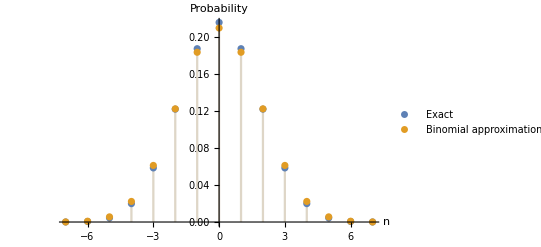

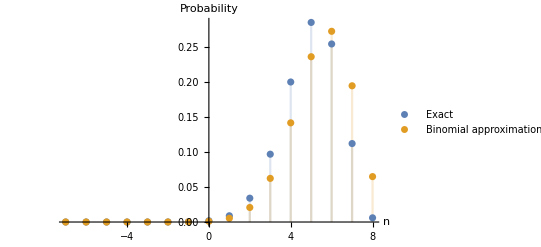

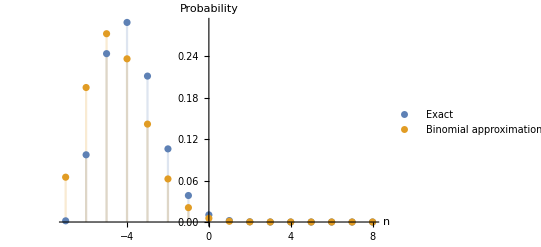

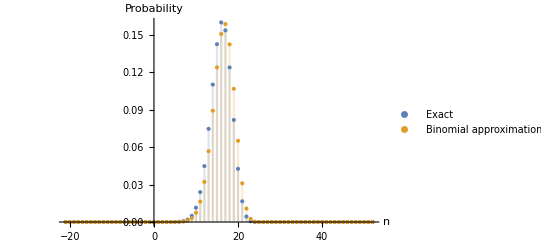

```mathematica
(* Plots for demonstration *)
(* Symmetric example *)
DiscretePlot[{p/.valsfast/.{x->2.2,y-> 1,z-> 1 },pbinomial/.valsfast/.{x->2.2,y-> 1,z-> 1 }},{n,nminfast/.valsfast/.{x->2.2,y-> 1,z-> 1 },nmaxfast/.valsfast/.{x->2.2,y-> 1,z-> 1 }},AxesLabel->{"n","Probability"},PlotLegends->Placed[{"Exact","Binomial approximation"},{0.5,0.5}],BaseStyle->FontSize-> 30]
(* non symmetric example *)
DiscretePlot[{p/.valsfast/.{x->2.2,y-> 3,z-> 5 },pbinomial/.valsfast/.{x->2.2,y-> 3,z-> 5 }},{n,nminfast/.valsfast/.{x->2.2,y-> 3,z-> 5 },nmaxfast/.valsfast/.{x->2.2,y-> 3,z-> 5 }},AxesLabel->{"n","Probability"},PlotLegends->Placed[{"Exact","Binomial approximation"},{0.5,0.5}],BaseStyle->FontSize-> 30]
DiscretePlot[{p/.valsfast/.{x->2.2,y-> 3,z-> 0.2 },pbinomial/.valsfast/.{x->2.2,y-> 3,z-> 0.2}},{n,nminfast/.valsfast/.{x->2.2,y-> 3,z-> 5 },nmaxfast/.valsfast/.{x->2.2,y-> 3,z-> 0.2 }},AxesLabel->{"n","Probability"},PlotLegends->Placed[{"Exact","Binomial approximation"},{0.5,0.5}],BaseStyle->FontSize-> 30]
(* large v example *)
 DiscretePlot[{p/.valsfast/.{x->5,y-> 3,z-> 5},pbinomial/.valsfast/.{x->5,y-> 3,z-> 5 }},{n,nminfast/.valsfast/.{x->5,y-> 3,z-> 5 },nmaxfast/.valsfast/.{x->10,y-> 3,z-> 0.2 }},AxesLabel->{"n","Probability"},PlotLegends->Placed[{"Exact","Binomial approximation"},{0.5,0.5}],BaseStyle->FontSize->30, PlotRange-> Full]
```

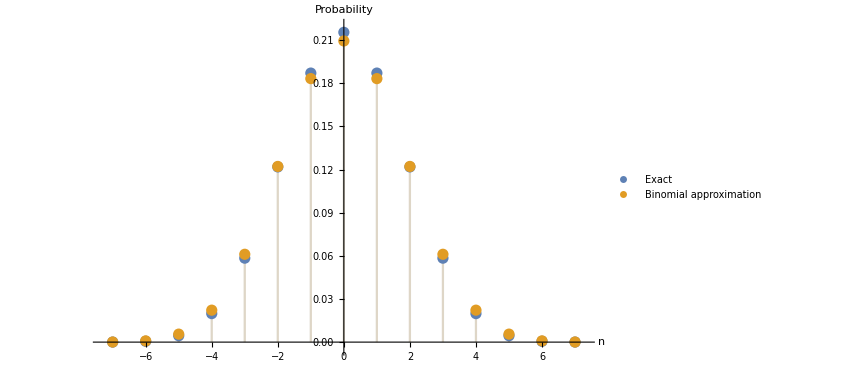

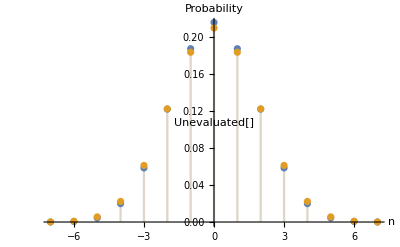

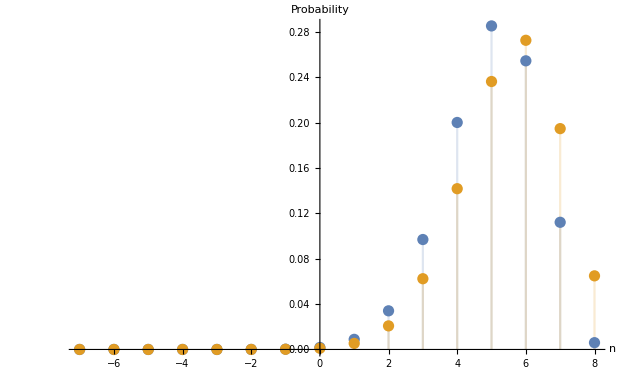

-Graphics-

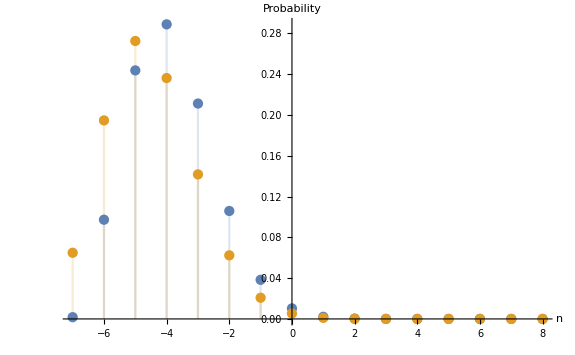

-Graphics-

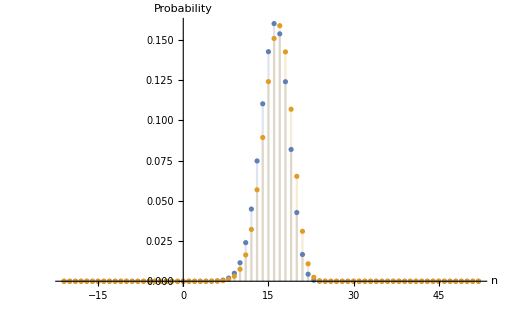

-Graphics-

```mathematica
(* Explicit Expression *)
Simplify[p/.{α-> αvalfast,β-> βvalfast}]
```

((-1)^(n-nmin) (R2/R1)^n Pochhammer[((C1+C2) e+CG e+2 (C1+C2) e nmin-2 C2 (C1+C2+CG) V-2 CG (C1 VL+C2 VR-(C1+C2) ϕ))/(2 (C1+C2) e),n-nmin])/((((-1)^(nmax-nmin) (R2/R1)^(1+nmax) Gamma[((C1+C2) e-CG e+2 (C1+C2) e nmin+2 C1 (C1+C2+CG) V-2 CG (C1 VL+C2 VR-(C1+C2) ϕ))/(2 (C1+C2) e)] Gamma[(3 (C1+C2) e+CG e+2 (C1+C2) e nmax-2 C2 (C1+C2+CG) V-2 CG (C1 VL+C2 VR-(C1+C2) ϕ))/(2 (C1+C2) e)] Hypergeometric2F1[1,(3 (C1+C2) e+CG e+2 (C1+C2) e nmax-2 C2 (C1+C2+CG) V-2 CG (C1 VL+C2 VR-(C1+C2) ϕ))/(2 (C1+C2) e),(3 (C1+C2) e-CG e+2 (C1+C2) e nmax+2 C1 (C1+C2+CG) V-2 CG (C1 VL+C2 VR-(C1+C2) ϕ))/(2 (C1+C2) e),-R2/R1])/(Gamma[(3 (C1+C2) e-CG e+2 (C1+C2) e nmax+2 C1 (C1+C2+CG) V-2 CG (C1 VL+C2 VR-(C1+C2) ϕ))/(2 (C1+C2) e)] Gamma[((C1+C2) e+CG e+2 (C1+C2) e nmin-2 C2 (C1+C2+CG) V-2 CG (C1 VL+C2 VR-(C1+C2) ϕ))/(2 (C1+C2) e)])+(R2/R1)^nmin Hypergeometric2F1[1,((C1+C2) e+CG e+2 (C1+C2) e nmin-2 C2 (C1+C2+CG) V-2 CG (C1 VL+C2 VR-(C1+C2) ϕ))/(2 (C1+C2) e),((C1+C2) e-CG e+2 (C1+C2) e nmin+2 C1 (C1+C2+CG) V-2 CG (C1 VL+C2 VR-(C1+C2) ϕ))/(2 (C1+C2) e),-R2/R1]) Pochhammer[((C1+C2) e-CG e+2 (C1+C2) e nmin+2 C1 (C1+C2+CG) V-2 CG (C1 VL+C2 VR-(C1+C2) ϕ))/(2 (C1+C2) e),n-nmin])

```mathematica
(* Small v*)
pfastsmallvnmin=Simplify[psmallv/.{n-> nmin,α-> αvalfast,β-> βvalfast}]
pfastsmallvnmax=Simplify[psmallv/.{n-> nmin+1,α-> αvalfast,β-> βvalfast}]
```

(R1 (-CG e+2 C1^2 V+C1 (e+2 e nmin+2 C2 V+2 CG (V-VL+ϕ))+C2 (e+2 e nmin+2 CG (-VR+ϕ))))/(C2 e (1+2 nmin) (R1-R2)-CG e (R1+R2)+2 C1^2 R1 V+2 C2^2 R2 V+2 C2 CG (R2 (V+VR-ϕ)+R1 (-VR+ϕ))+C1 (e (1+2 nmin) (R1-R2)+2 (C2 (R1+R2) V+CG R2 (VL-ϕ)+CG R1 (V-VL+ϕ))))

-(R2 (CG e-2 C2^2 V+C2 (e+2 e nmin-2 CG (V+VR-ϕ))+C1 (e+2 e nmin-2 C2 V-2 CG VL+2 CG ϕ)))/(C2 e (1+2 nmin) (R1-R2)-CG e (R1+R2)+2 C1^2 R1 V+2 C2^2 R2 V+2 C2 CG (R2 (V+VR-ϕ)+R1 (-VR+ϕ))+C1 (e (1+2 nmin) (R1-R2)+2 (C2 (R1+R2) V+CG R2 (VL-ϕ)+CG R1 (V-VL+ϕ))))

### Current

```mathematica
(* Small V *)
currentsmallVfast = Simplify[V/(R1+R2)-e/((C1+C2)(R1+R2))(1-pfastsmallvnmax (Wmaxfast/.nmax-> nmin+1)-pfastsmallvnmin Wminfast)]
```

(-2 C1^3 V (e+2 e nmin-2 C2 V-2 CG VL+2 CG ϕ)-C1^2 ((e+2 e nmin)^2-8 C2^2 V^2+2 C2 e (V+2 nmin V)-4 C2 CG V (2 V+VR-ϕ)-4 CG^2 (VL-ϕ) (V-VL+ϕ)+4 CG e (V+nmin V-VL-2 nmin VL+ϕ+2 nmin ϕ))+(-CG e+2 C2^2 V-C2 (e+2 e nmin-2 CG (V+VR-ϕ))) (-CG e+C2 (e+2 e nmin+2 CG (-VR+ϕ)))+2 C1 (-CG^2 e V+2 C2^3 V^2+C2^2 V (e+2 e nmin+2 CG (2 V-VL+ϕ))-C2 ((e+2 e nmin)^2+2 CG e (V-(1+2 nmin) (VL+VR-2 ϕ))-2 CG^2 (V^2+V (-VL+VR)+2 (VL-ϕ) (-VR+ϕ)))))/(2 (C1+C2) (C1+C2+CG) (C2 e (1+2 nmin) (R1-R2)-CG e (R1+R2)+2 C1^2 R1 V+2 C2^2 R2 V+2 C2 CG (R2 (V+VR-ϕ)+R1 (-VR+ϕ))+C1 (e (1+2 nmin) (R1-R2)+2 (C2 (R1+R2) V+CG R2 (VL-ϕ)+CG R1 (V-VL+ϕ)))))

```mathematica
(* Full solution *)
Manipulate[Plot[current/.valsfast/.{x-> Vext,y-> Cratio,z-> Rratio },{Vext,0,2}],{Cratio,0.1,10},{Rratio,0.1,10}]
```

ReplaceAll::reps: {valsfast} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

ReplaceAll::reps: {valsfast} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

ReplaceAll::reps: {valsfast} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

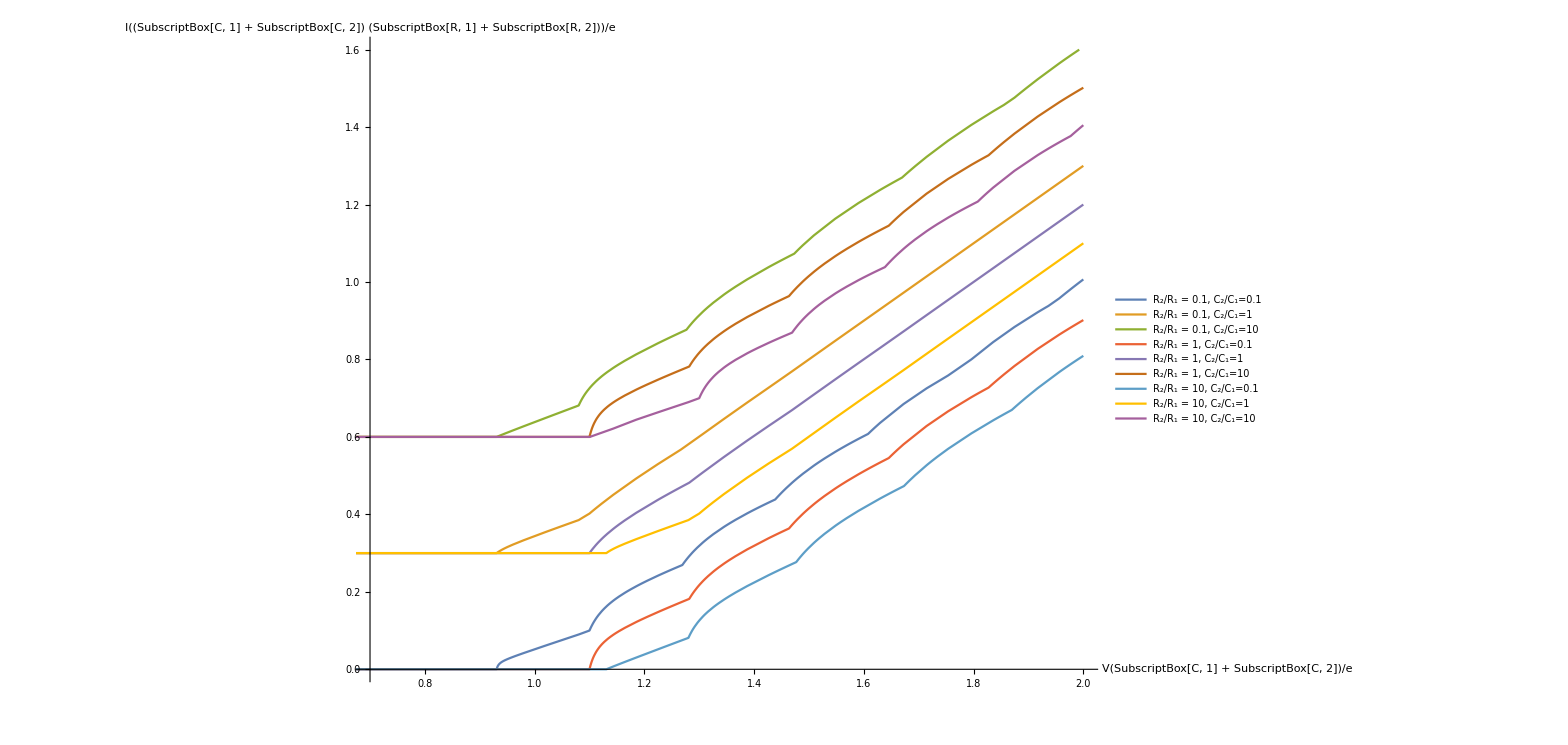

```mathematica
(* Example *)
Plot[{current/.valsfast/.{x-> Vext,y-> 0.1,z-> 0.1 },0.3+current/.valsfast/.{x-> Vext,y-> 0.1,z-> 1 },0.6+current/.valsfast/.{x-> Vext,y-> 0.1,z-> 10},current/.valsfast/.{x-> Vext-0.1,y-> 1,z-> 0.1 },0.3+current/.valsfast/.{x-> Vext-0.1,y-> 1,z-> 1 },0.6+current/.valsfast/.{x-> Vext-0.1,y-> 1,z-> 10},current/.valsfast/.{x-> Vext-0.2,y-> 10,z-> 0.1 },0.3+current/.valsfast/.{x-> Vext-0.2,y-> 10,z-> 1 },0.6+current/.valsfast/.{x-> Vext-0.2,y-> 10,z-> 10}},{Vext,0,2},AxesLabel->{"V(SubscriptBox[C, 1] + SubscriptBox[C, 2])/e","I((SubscriptBox[C, 1]  + SubscriptBox[C, 2]) (SubscriptBox[R, 1] + SubscriptBox[R, 2]))/e"},BaseStyle->FontSize-> 30, PlotRange->{{0.7,2},{0,1.6}}, PlotLegends->Placed[LineLegend[{"R_2/R_1 = 0.1, C_2/C_1=0.1","R_2/R_1 = 0.1, C_2/C_1=1","R_2/R_1 = 0.1, C_2/C_1=10","R_2/R_1 = 1, C_2/C_1=0.1","R_2/R_1 = 1, C_2/C_1=1","R_2/R_1 = 1, C_2/C_1=10","R_2/R_1 = 10, C_2/C_1=0.1","R_2/R_1 = 10, C_2/C_1=1","R_2/R_1 = 10, C_2/C_1=10"}, LabelStyle-> {Black,20}, LegendLayout->{"Row",4}],{0.35,0.85}]]
```

Slow Relaxation

### Probability function

```mathematica
(* defining parameters *) 
αvalslow = (C2 V)/e-QG/e-1/2;
βvalslow = (C1 V)/e+QG/e+1/2;
nminslow= Floor[-C1/e V+1/2-QG/e];
nmaxslow=Ceiling[C2/e V-1/2-QG/e];
```

```mathematica
(* Defining values *)
constvalsslow={C1-> 1/(y+1),C2->y/(y+1),CG->1,V->x, VL-> x/2,VR-> -x/2,e-> 1,R1->1/(z+1),R2-> z/(z+1),ϕ-> 0.5, QG-> q};
nminvalslow=nminslow/.constvalsslow;
nmaxvalslow=nmaxslow/.constvalsslow;
Wmaxvalslow = Wmax/.{nmax-> nmaxvalslow}/.constvalsslow;
Wminvalslow = Wmin/.{nmin-> nminvalslow}/.constvalsslow;
valsslow=Join[constvalsslow,{nmin->nminvalslow,nmax-> nmaxvalslow, α-> αvalslow/.constvalsslow, β-> βvalslow/.constvalsslow, Wmin-> Wminvalslow,Wmax-> Wmaxvalslow}];
```

```mathematica
(* Plotting Probability Function *)
Manipulate[DiscretePlot[{p/.valsslow/.{x-> Vext,y-> Cratio,z-> Rratio , q-> gateCharge},pbinomial/.valsslow/.{x-> Vext,y-> Cratio,z-> Rratio , q-> gateCharge}},{n,nminslow/.valsslow/.{x-> Vext,y-> Cratio,z-> Rratio , q-> gateCharge},nmaxslow/.valsslow/.{x-> Vext,y-> Cratio,z-> Rratio, q-> gateCharge }}],{Vext,0,10},{Cratio,0.1,10},{Rratio,0.1,10}, { gateCharge,-1,1}]
```

ReplaceAll::reps: {valsslow} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

DiscretePlot::iterb: Iterator {n,nminslow/.valsslow/.{x→FE`Vext$$24,y→FE`Cratio$$24,z→FE`Rratio$$24,q→FE`gateCharge$$24},nmaxslow/.valsslow/.{x→FE`Vext$$24,y→FE`Cratio$$24,z→FE`Rratio$$24,q→FE`gateCharge$$24}} does not have appropriate bounds.

ReplaceAll::reps: {valsslow} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

DiscretePlot::iterb: Iterator {n,nminslow/.valsslow/.{x→FE`Vext$$24,y→FE`Cratio$$24,z→FE`Rratio$$24,q→FE`gateCharge$$24},nmaxslow/.valsslow/.{x→FE`Vext$$24,y→FE`Cratio$$24,z→FE`Rratio$$24,q→FE`gateCharge$$24}} does not have appropriate bounds.

ReplaceAll::reps: {valsslow} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

DiscretePlot::iterb: Iterator {n,nminslow/.valsslow/.{x→FE`Vext$$24,y→FE`Cratio$$24,z→FE`Rratio$$24,q→FE`gateCharge$$24},nmaxslow/.valsslow/.{x→FE`Vext$$24,y→FE`Cratio$$24,z→FE`Rratio$$24,q→FE`gateCharge$$24}} does not have appropriate bounds.

ReplaceAll::reps: {valsslow} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

DiscretePlot::iterb: Iterator {n,nminslow/.valsslow/.{x→FE`Vext$$28,y→FE`Cratio$$28,z→FE`Rratio$$28,q→FE`gateCharge$$28},nmaxslow/.valsslow/.{x→FE`Vext$$28,y→FE`Cratio$$28,z→FE`Rratio$$28,q→FE`gateCharge$$28}} does not have appropriate bounds.

ReplaceAll::reps: {valsslow} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

DiscretePlot::iterb: Iterator {n,nminslow/.valsslow/.{x→FE`Vext$$28,y→FE`Cratio$$28,z→FE`Rratio$$28,q→FE`gateCharge$$28},nmaxslow/.valsslow/.{x→FE`Vext$$28,y→FE`Cratio$$28,z→FE`Rratio$$28,q→FE`gateCharge$$28}} does not have appropriate bounds.

ReplaceAll::reps: {valsslow} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

DiscretePlot::iterb: Iterator {n,nminslow/.valsslow/.{x→FE`Vext$$28,y→FE`Cratio$$28,z→FE`Rratio$$28,q→FE`gateCharge$$28},nmaxslow/.valsslow/.{x→FE`Vext$$28,y→FE`Cratio$$28,z→FE`Rratio$$28,q→FE`gateCharge$$28}} does not have appropriate bounds.

ReplaceAll::reps: {valsslow} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

DiscretePlot::iterb: Iterator {n,nminslow/.valsslow/.{x→FE`Vext$$20,y→FE`Cratio$$20,z→FE`Rratio$$20,q→FE`gateCharge$$20},nmaxslow/.valsslow/.{x→FE`Vext$$20,y→FE`Cratio$$20,z→FE`Rratio$$20,q→FE`gateCharge$$20}} does not have appropriate bounds.

ReplaceAll::reps: {valsslow} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

DiscretePlot::iterb: Iterator {n,nminslow/.valsslow/.{x→FE`Vext$$32,y→FE`Cratio$$32,z→FE`Rratio$$32,q→FE`gateCharge$$32},nmaxslow/.valsslow/.{x→FE`Vext$$32,y→FE`Cratio$$32,z→FE`Rratio$$32,q→FE`gateCharge$$32}} does not have appropriate bounds.

ReplaceAll::reps: {valsslow} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

DiscretePlot::iterb: Iterator {n,nminslow/.valsslow/.{x→FE`Vext$$32,y→FE`Cratio$$32,z→FE`Rratio$$32,q→FE`gateCharge$$32},nmaxslow/.valsslow/.{x→FE`Vext$$32,y→FE`Cratio$$32,z→FE`Rratio$$32,q→FE`gateCharge$$32}} does not have appropriate bounds.

ReplaceAll::reps: {valsslow} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

DiscretePlot::iterb: Iterator {n,nminslow/.valsslow/.{x→FE`Vext$$32,y→FE`Cratio$$32,z→FE`Rratio$$32,q→FE`gateCharge$$32},nmaxslow/.valsslow/.{x→FE`Vext$$32,y→FE`Cratio$$32,z→FE`Rratio$$32,q→FE`gateCharge$$32}} does not have appropriate bounds.

ReplaceAll::reps: {valsslow} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

DiscretePlot::iterb: Iterator {n,nminslow/.valsslow/.{x→FE`Vext$$32,y→FE`Cratio$$32,z→FE`Rratio$$32,q→FE`gateCharge$$32},nmaxslow/.valsslow/.{x→FE`Vext$$32,y→FE`Cratio$$32,z→FE`Rratio$$32,q→FE`gateCharge$$32}} does not have appropriate bounds.

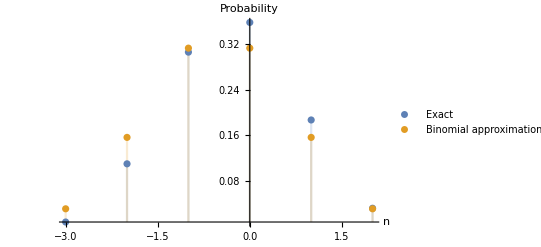

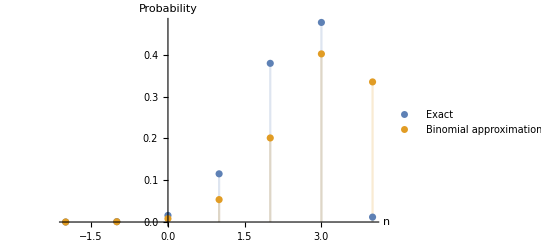

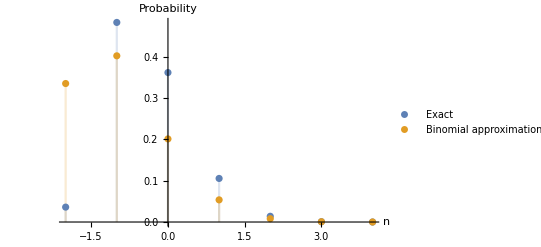

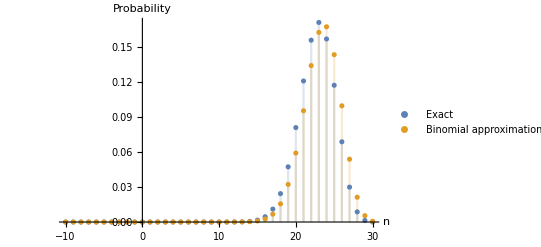

```mathematica
(* Examples *)
DiscretePlot[{p/.valsslow/.{x->5.1,y-> 1,z->1  ,q-> 0.3},pbinomial/.valsslow/.{x->5.1,y-> 1,z-> 1,q -> 0.3}},{n,nminslow/.valsslow/.{x->5.1,y-> 1,z-> 1 ,q-> 0.3},nmaxslow/.valsslow/.{x->5.1,y-> 1,z-> 1 ,q-> 0.3}},AxesLabel->{"n","Probability"},PlotLegends->Placed[{"Exact","Binomial approximation"},{0.5,0.5}],BaseStyle->FontSize-> 30, PlotRange-> Full]
DiscretePlot[{p/.valsslow/.{x->5.1,y-> 3,z-> 5 ,q-> 0.3},pbinomial/.valsslow/.{x->5.1,y-> 3,z-> 5 ,q-> 0.3}},{n,nminslow/.valsslow/.{x->5.1,y-> 3,z-> 5,q-> 0.3},nmaxslow/.valsslow/.{x->5.1,y-> 3,z-> 5 ,q-> 0.3}},AxesLabel->{"n","Probability"},PlotLegends->Placed[{"Exact","Binomial approximation"},{0.5,0.5}],BaseStyle->FontSize-> 30, PlotRange-> Full]
DiscretePlot[{p/.valsslow/.{x->5.1,y-> 3,z-> 0.2 ,q-> 0.3},pbinomial/.valsslow/.{x->5.1,y-> 3,z-> 0.2,q-> 0.3}},{n,nminslow/.valsslow/.{x->5.1,y-> 3,z-> 0.2 ,q-> 0.3},nmaxslow/.valsslow/.{x->5.1,y->3,z-> 0.2 ,q-> 0.3}},AxesLabel->{"n","Probability"},PlotLegends->Placed[{"Exact","Binomial approximation"},{0.5,0.5}],BaseStyle->FontSize-> 30, PlotRange-> Full]
DiscretePlot[{p/.valsslow/.{x->40,y-> 3,z-> 5 ,q-> 0.3},pbinomial/.valsslow/.{x->40,y-> 3,z-> 5,q->  0.3}},{n,nminslow/.valsslow/.{x->40,y-> 3,z-> 5 ,q-> 0.3},nmaxslow/.valsslow/.{x->40,y-> 3,z-> 5 ,q-> 0.3}},AxesLabel->{"n","Probability"},PlotLegends->Placed[{"Exact","Binomial approximation"},{0.5,0.5}],BaseStyle->FontSize-> 30, PlotRange-> Full]
```

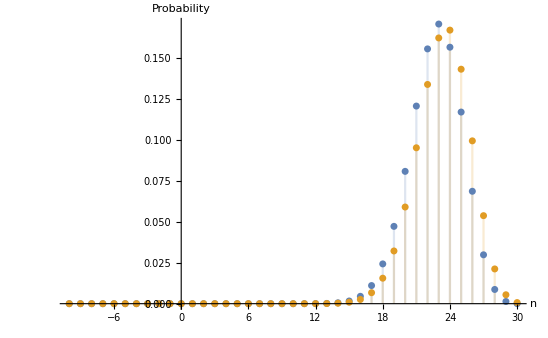

-Graphics-

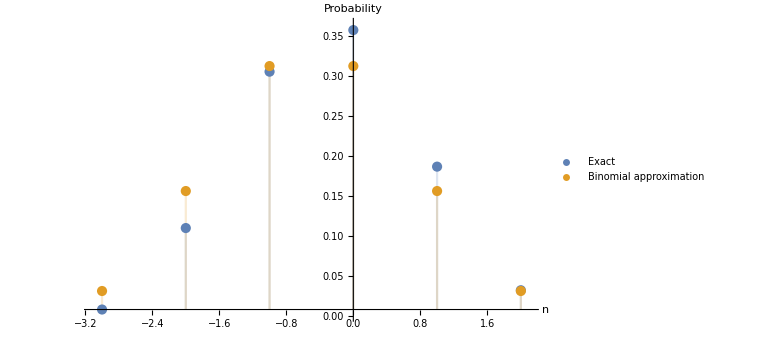

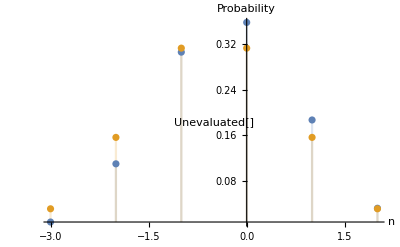

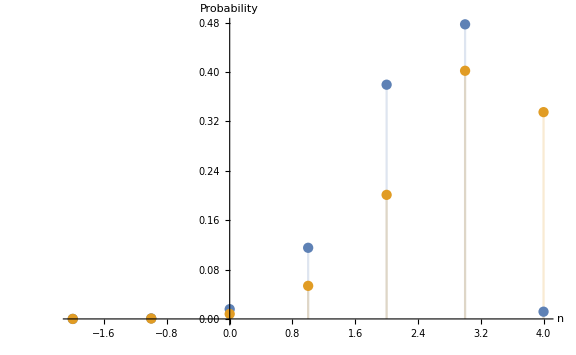

-Graphics-

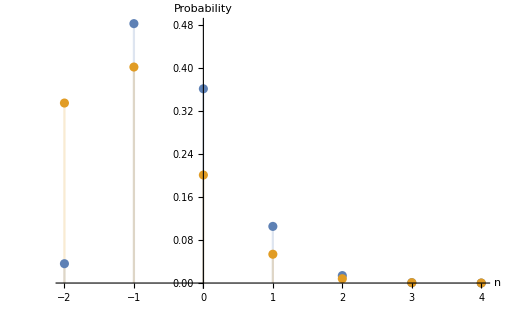

-Graphics-

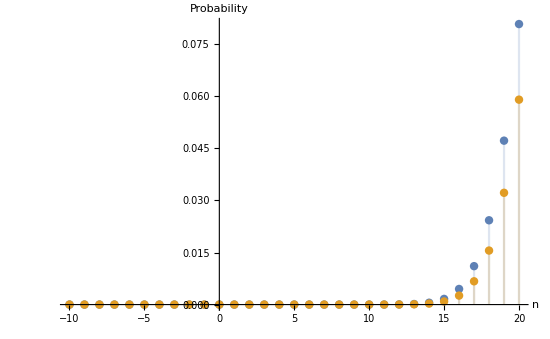

-Graphics-

```mathematica
(* Explicit Expression *)
Simplify[p/.{α-> αvalslow,β-> βvalslow}]
```

((-1)^(n-nmin) (R2/R1)^n Pochhammer[nmin+(e+2 QG-2 C2 V)/(2 e),n-nmin])/(((R2/R1)^nmin Hypergeometric2F1[1,nmin+(e+2 QG-2 C2 V)/(2 e),1/2+nmin+QG/e+(C1 V)/e,-R2/R1]+((-1)^(nmax-nmin) (R2/R1)^(1+nmax) Gamma[1/2+nmin+QG/e+(C1 V)/e] Gamma[3/2+nmax+(QG-C2 V)/e] Hypergeometric2F1[1,3/2+nmax+(QG-C2 V)/e,3/2+nmax+(QG+C1 V)/e,-R2/R1])/(Gamma[3/2+nmax+(QG+C1 V)/e] Gamma[nmin+(e+2 QG-2 C2 V)/(2 e)])) Pochhammer[1/2+nmin+QG/e+(C1 V)/e,n-nmin])

```mathematica
(* Small V *)
pslowsmallvnmin=Simplify[psmallv/.{n-> nmin,α-> αvalslow,β-> βvalslow}]
pslowsmallvnmax=Simplify[psmallv/.{n-> nmin+1,α-> αvalslow,β-> βvalslow}]
```

(R1 (e+2 e nmin+2 (QG+C1 V)))/(e (1+2 nmin) (R1-R2)+2 (QG R1-QG R2+C1 R1 V+C2 R2 V))

-(R2 (e+2 e nmin+2 QG-2 C2 V))/(e (1+2 nmin) (R1-R2)+2 (QG R1-QG R2+C1 R1 V+C2 R2 V))

## Steady state QG

### Voltage on island

```mathematica
(* Definitions *)
U = (navg e+QG + C1 V/2- C2 V/2)/(C1+C2);

Ubinomial=V (R2 C2-R1 C1)/((C1+C2)(R1+R2))+(C1 VL + C2 VR)/(C1+C2)-e/2(R2-R1)/((C1+C2)(R1+R2));
Usmallv = Piecewise[{{(nmin e+QG + C1 V/2- C2 V/2)/(C1+C2),nmax≤nmin},{(navgsmallv e+QG + C1 V/2- C2 V/2)/(C1+C2),nmax>nmin}}];
Ufromgate=-QG/CG+ϕ;
```

```mathematica
(* Plotting voltage *)
Manipulate[Plot[{U/.valsslow/.{x-> Vext,y-> Cratio,z-> Rratio , q-> gateCharge, X-> gateCapacitance},Ufromgate/.valsslow/.{x-> Vext,y-> Cratio,z-> Rratio , q-> gateCharge}},
{gateCharge,-2,2}],{Vext,0,2},{Cratio,0.1,10},{Rratio,0.1,10}, {gateCapacitance,0.1,10}]
```

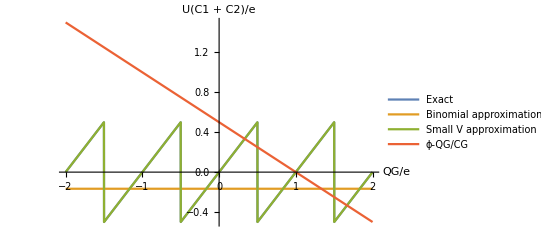

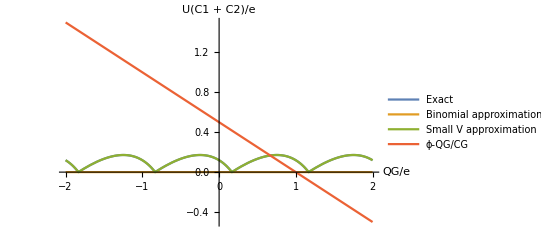

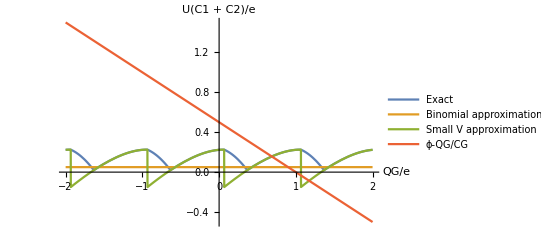

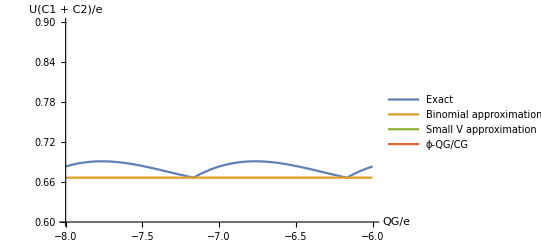

```mathematica
(* Examples *)
Plot[{U/.valsslow/.{x->0,y-> 2,z-> 2 , q-> gateCharge},Ubinomial/.valsslow/.{x-> 0,y-> 2,z-> 2 , q-> gateCharge}, Usmallv/.valsslow/.{x-> 0,y-> 2,z-> 2 , q-> gateCharge}, Ufromgate/.valsslow/.{x-> 0,y-> 2,z-> 2 , q-> gateCharge}},{gateCharge,-2,2},AxesLabel->{"QG/e","U(C1 + C2)/e"},PlotLegends->{"Exact","Binomial approximation","Small V approximation","ϕ-QG/CG"},BaseStyle->FontSize-> 16, PlotRange-> Full]
Plot[{U/.valsslow/.{x->1,y-> 2,z-> 2 , q-> gateCharge},Ubinomial/.valsslow/.{x-> 1,y-> 2,z-> 2 , q-> gateCharge}, Usmallv/.valsslow/.{x-> 1,y-> 2,z-> 2 , q-> gateCharge}, Ufromgate/.valsslow/.{x-> 1,y-> 2,z-> 2 , q-> gateCharge}},{gateCharge,-2,2},AxesLabel->{"QG/e","U(C1 + C2)/e"},PlotLegends->{"Exact","Binomial approximation","Small V approximation","ϕ-QG/CG"},BaseStyle->FontSize-> 16, PlotRange-> Full]
Plot[{U/.valsslow/.{x->1.3,y-> 2,z-> 2 , q-> gateCharge},Ubinomial/.valsslow/.{x-> 1.3,y-> 2,z-> 2 , q-> gateCharge}, Usmallv/.valsslow/.{x-> 1.3,y-> 2,z-> 2 , q-> gateCharge}, Ufromgate/.valsslow/.{x-> 1.3,y-> 2,z-> 2 , q-> gateCharge}},{gateCharge,-2,2},AxesLabel->{"QG/e","U(C1 + C2)/e"},PlotLegends->{"Exact","Binomial approximation","Small V approximation","ϕ-QG/CG"},BaseStyle->FontSize-> 16, PlotRange-> Full]
Plot[{U/.valsslow/.{x->5,y-> 2,z-> 2 , q-> gateCharge},Ubinomial/.valsslow/.{x-> 5,y-> 2,z-> 2 , q-> gateCharge}, Usmallv/.valsslow/.{x-> 5,y-> 2,z-> 2 , q-> gateCharge}, Ufromgate/.valsslow/.{x-> 5,y-> 2,z-> 2 , q-> gateCharge}},{gateCharge,-8,-6},AxesLabel->{"QG/e","U(C1 + C2)/e"},PlotLegends->{"Exact","Binomial approximation","Small V approximation","ϕ-QG/CG"},BaseStyle->FontSize-> 16, PlotRange-> {{-8,-6},{0.6,0.9}}]
```

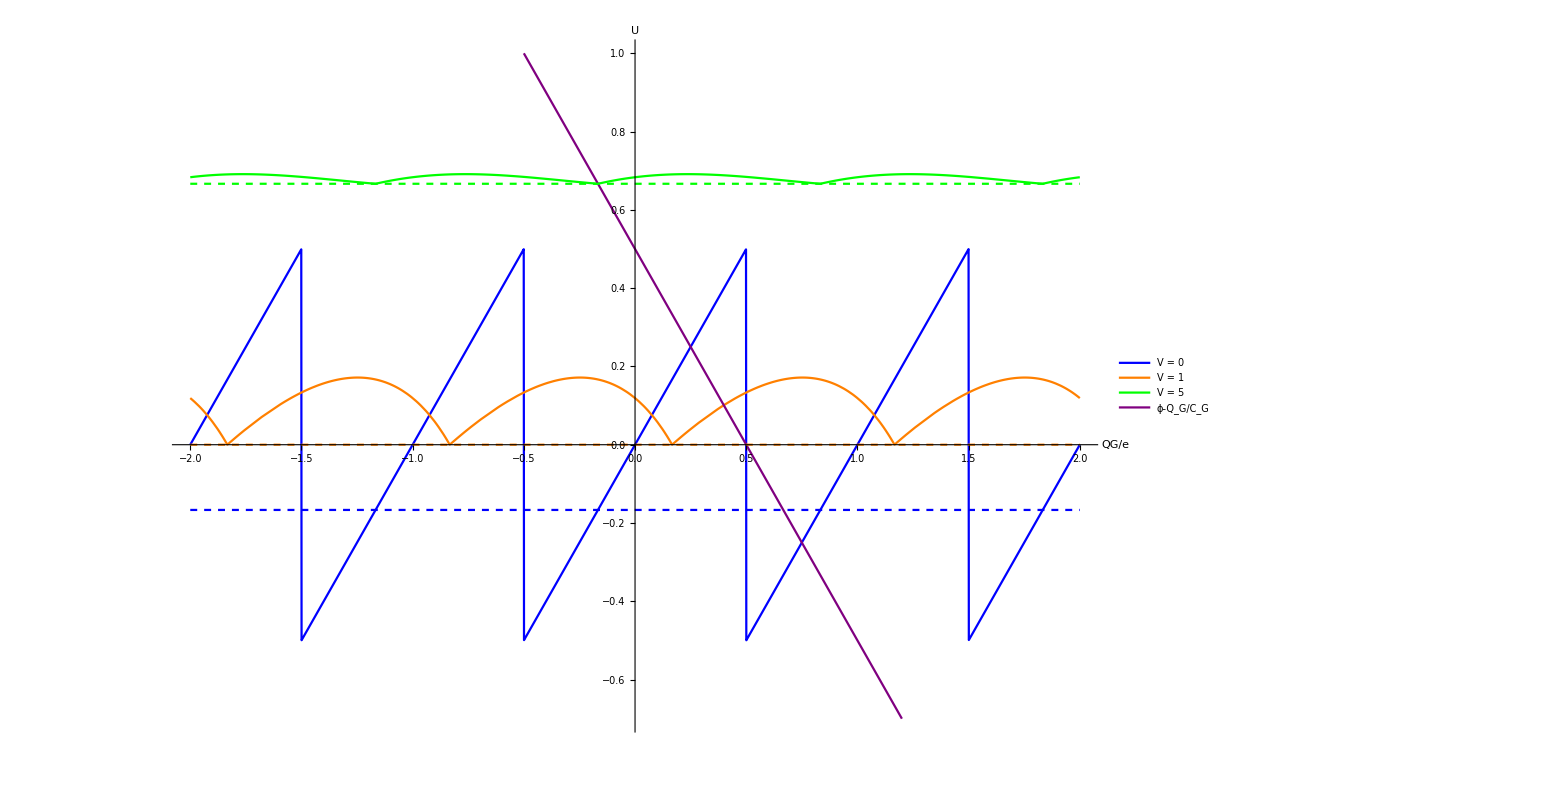

```mathematica
p1=Plot[{U/.valsslow/.{x->0,y-> 2,z-> 2 , q-> gateCharge},U/.valsslow/.{x->1,y-> 2,z-> 2 , q-> gateCharge},U/.valsslow/.{x->5,y-> 2,z-> 2 , q-> gateCharge},Ufromgate/.valsslow/.{x-> 0,y-> 2,z-> 2 , q-> gateCharge}},{gateCharge,-2,2},AxesLabel->{"QG/e","U"},BaseStyle->FontSize->30, PlotRange-> {{-2,2},{-0.7,1}}, PlotLegends->Placed[LineLegend[{"V = 0","V = 1","V = 5","ϕ-Q_G/C_G"}, LabelStyle-> {Black,30}, LegendLayout->"Row"],{0.75,0.9}], PlotStyle->{Blue,Orange,Green,Purple}];
p2=Plot[{Ubinomial/.valsslow/.{x->0,y-> 2,z-> 2 , q-> gateCharge},Ubinomial/.valsslow/.{x->1,y-> 2,z-> 2 , q-> gateCharge},Ubinomial/.valsslow/.{x->5,y-> 2,z-> 2 , q-> gateCharge}},{gateCharge,-2,2},AxesLabel->{"QG/e","U"},BaseStyle->FontSize-> 30, PlotRange-> {{-2,2},{-0.7,1}},PlotStyle->{{Blue,Dashed},{Orange,Dashed},{Green,Dashed}}];
Show[p1,p2]
```

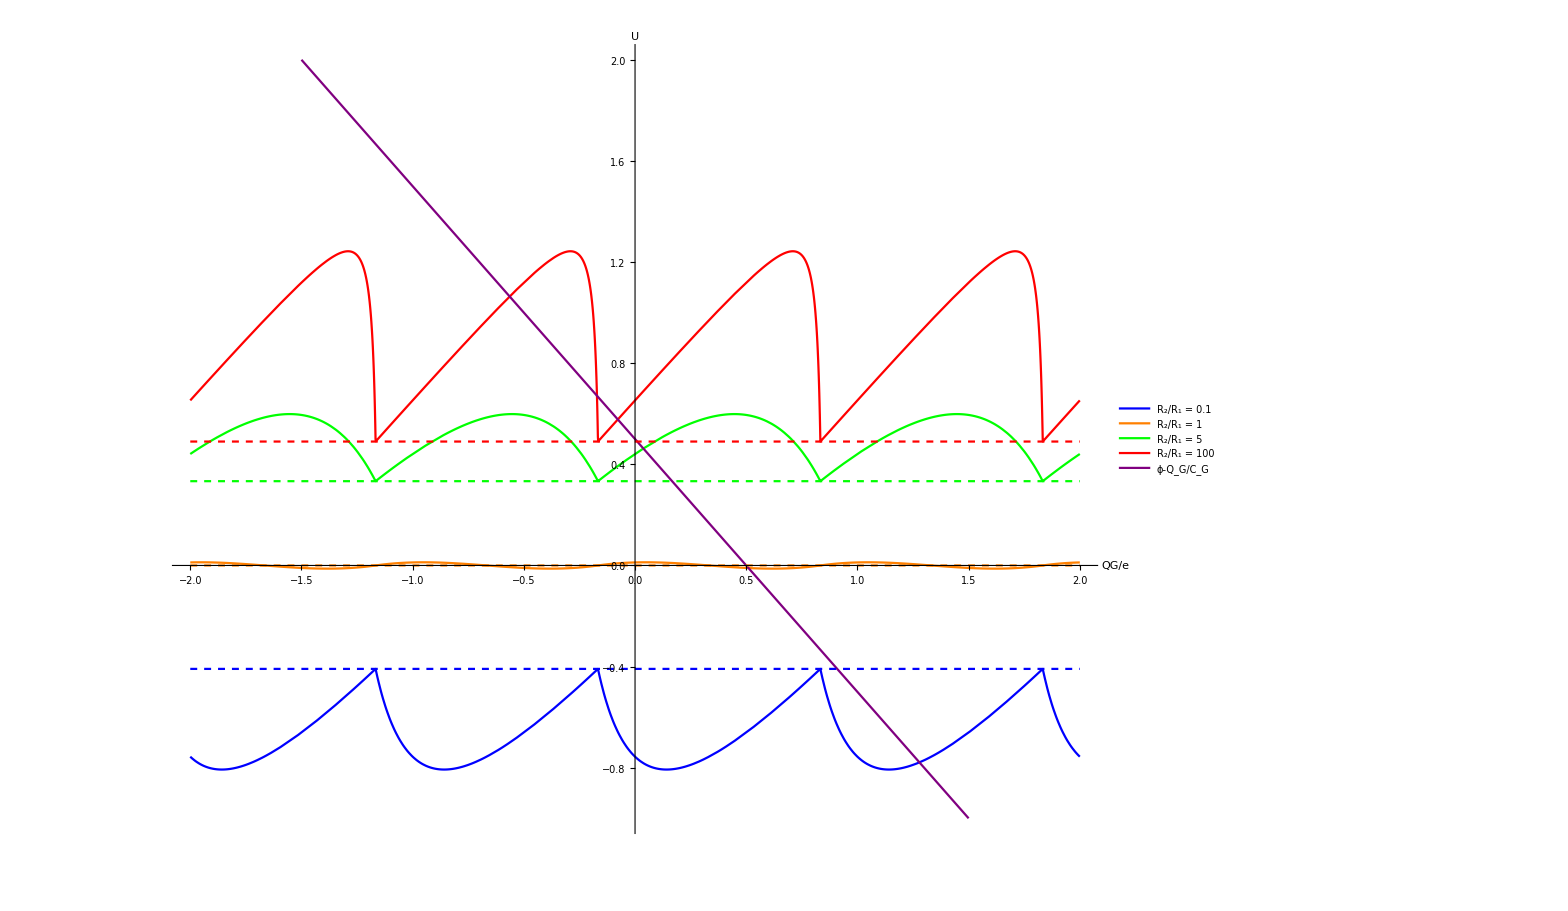

```mathematica
p1=Plot[{U/.valsslow/.{x->2,y-> 2,z-> 0.1 , q-> gateCharge},U/.valsslow/.{x->2,y-> 2,z-> 1 , q-> gateCharge},U/.valsslow/.{x->2,y-> 2,z-> 5 , q-> gateCharge},
U/.valsslow/.{x->2,y-> 2,z-> 100 , q-> gateCharge},Ufromgate/.valsslow/.{x-> 0,z-> 2 , q-> gateCharge}},{gateCharge,-2,2},AxesLabel->{"QG/e","U"},BaseStyle->FontSize-> 30, PlotRange-> {{-2,2},{-1,2}},PlotLegends->Placed[LineLegend[{"R_2/R_1 = 0.1","R_2/R_1 = 1","R_2/R_1 = 5","R_2/R_1 = 100","ϕ-Q_G/C_G"}, LabelStyle-> {Black,30}, LegendLayout->{"Row",2}],{0.4,0.9}], PlotStyle->{Blue,Orange,Green,Red,Purple}];
p2=Plot[{Ubinomial/.valsslow/.{x->2,y-> 2,z-> 0.1 , q-> gateCharge},Ubinomial/.valsslow/.{x->2,y-> 2,z-> 1 , q-> gateCharge},Ubinomial/.valsslow/.{x->2,y-> 2,z-> 5 , q-> gateCharge},
Ubinomial/.valsslow/.{x->2,y-> 2,z-> 100 , q-> gateCharge}},{gateCharge,-2,2},AxesLabel->{"QG/e","U"},BaseStyle->FontSize-> 30, PlotRange-> {{-2,2},{-1,2}},PlotStyle->{{Blue,Dashed},{Orange,Dashed},{Green,Dashed},{Red,Dashed}}];
Show[p1,p2]
```

```mathematica
(* Steady state QG for small voltage *)
QGsteadysmallv1=QG/.Solve[(Usmallv/.{nmin-> 0,nmax-> 1,α-> αvalslow,β-> βvalslow})==Ufromgate,QG];
QGsteadysmallv2=QG/.Solve[(Usmallv/.{nmin-> -1,nmax-> 0,α-> αvalslow,β-> βvalslow})==Ufromgate,QG];
```

### Current For small voltage

```mathematica
Wmaxslow=Wmax/.{nmax-> 1,QG-> QGsteadysmallv1};
Wminslow=Wmin/.{nmin-> 0,QG-> QGsteadysmallv1};
currentsmallVslow =Simplify[V/(R1+R2)-e/((C1+C2)(R1+R2))(1-(pslowsmallvnmax/.{nmin-> 0,QG-> QGsteadysmallv1}) Wmaxslow-(pslowsmallvnmin/.{nmin-> 0,QG-> QGsteadysmallv1}) Wminslow)]
```

{1/(R1+R2)(V-(R1 (C1 e R1+C2 e R1+CG e R1-C1 e R2-C2 e R2+CG e R2+2 C1^2 R1 V+2 C1 C2 R1 V+C1 CG R1 V+C2 CG R1 V-4 C1^2 R2 V-6 C1 C2 R2 V-2 C2^2 R2 V-3 C1 CG R2 V-3 C2 CG R2 V+2 C1 CG R1 ϕ+2 C2 CG R1 ϕ-2 C1 CG R2 ϕ-2 C2 CG R2 ϕ-√(4 CG (C1+C2+CG) (R1-R2) (2 e^2 R2-2 (C1 R1+C2 R2) V (C1 (V-2 ϕ)-C2 (V+2 ϕ))+e (-C1 (R1-R2) (V-2 ϕ)+C2 (R1 V-5 R2 V+2 R1 ϕ-2 R2 ϕ)))+(CG e (R1-3 R2)+C2 e (R1-R2)+2 C1^2 R1 V+2 C2^2 R2 V+C2 CG (-R1 (V+2 ϕ)+R2 (3 V+2 ϕ))+C1 (e (R1-R2)+2 C2 (R1+R2) V+CG (3 R1 V-R2 V-2 R1 ϕ+2 R2 ϕ)))^2)) (-3 C1 e R1-3 C2 e R1-3 CG e R1+3 C1 e R2+3 C2 e R2+5 CG e R2+2 C1^2 R1 V+2 C1 C2 R1 V+C1 CG R1 V+C2 CG R1 V-4 C1^2 R2 V-6 C1 C2 R2 V-2 C2^2 R2 V-3 C1 CG R2 V-3 C2 CG R2 V+2 C1 CG R1 ϕ+2 C2 CG R1 ϕ-2 C1 CG R2 ϕ-2 C2 CG R2 ϕ-√(4 CG (C1+C2+CG) (R1-R2) (2 e^2 R2-2 (C1 R1+C2 R2) V (C1 (V-2 ϕ)-C2 (V+2 ϕ))+e (-C1 (R1-R2) (V-2 ϕ)+C2 (R1 V-5 R2 V+2 R1 ϕ-2 R2 ϕ)))+(CG e (R1-3 R2)+C2 e (R1-R2)+2 C1^2 R1 V+2 C2^2 R2 V+C2 CG (-R1 (V+2 ϕ)+R2 (3 V+2 ϕ))+C1 (e (R1-R2)+2 C2 (R1+R2) V+CG (3 R1 V-R2 V-2 R1 ϕ+2 R2 ϕ)))^2))+4 (C1+C2+CG) e (R1-R2)^2 (C1 e R1+C2 e R1+CG e R1-C1 e R2-C2 e R2+CG e R2+2 C1^2 R1 V+2 C1 C2 R1 V+C1 CG R1 V+C2 CG R1 V+2 C1 C2 R2 V+2 C2^2 R2 V+C1 CG R2 V+C2 CG R2 V+2 C1 CG R1 ϕ+2 C2 CG R1 ϕ-2 C1 CG R2 ϕ-2 C2 CG R2 ϕ-√(4 CG (C1+C2+CG) (R1-R2) (2 e^2 R2-2 (C1 R1+C2 R2) V (C1 (V-2 ϕ)-C2 (V+2 ϕ))+e (-C1 (R1-R2) (V-2 ϕ)+C2 (R1 V-5 R2 V+2 R1 ϕ-2 R2 ϕ)))+(CG e (R1-3 R2)+C2 e (R1-R2)+2 C1^2 R1 V+2 C2^2 R2 V+C2 CG (-R1 (V+2 ϕ)+R2 (3 V+2 ϕ))+C1 (e (R1-R2)+2 C2 (R1+R2) V+CG (3 R1 V-R2 V-2 R1 ϕ+2 R2 ϕ)))^2))+R2 (-C1 e R1-C2 e R1-CG e R1+C1 e R2+C2 e R2-CG e R2+2 C1^2 R1 V+6 C1 C2 R1 V+4 C2^2 R1 V+3 C1 CG R1 V+3 C2 CG R1 V-2 C1 C2 R2 V-2 C2^2 R2 V-C1 CG R2 V-C2 CG R2 V-2 C1 CG R1 ϕ-2 C2 CG R1 ϕ+2 C1 CG R2 ϕ+2 C2 CG R2 ϕ+√(4 CG (C1+C2+CG) (R1-R2) (2 e^2 R2-2 (C1 R1+C2 R2) V (C1 (V-2 ϕ)-C2 (V+2 ϕ))+e (-C1 (R1-R2) (V-2 ϕ)+C2 (R1 V-5 R2 V+2 R1 ϕ-2 R2 ϕ)))+(CG e (R1-3 R2)+C2 e (R1-R2)+2 C1^2 R1 V+2 C2^2 R2 V+C2 CG (-R1 (V+2 ϕ)+R2 (3 V+2 ϕ))+C1 (e (R1-R2)+2 C2 (R1+R2) V+CG (3 R1 V-R2 V-2 R1 ϕ+2 R2 ϕ)))^2)) (-5 C1 e R1-5 C2 e R1-5 CG e R1+5 C1 e R2+5 C2 e R2+3 CG e R2+2 C1^2 R1 V+6 C1 C2 R1 V+4 C2^2 R1 V+3 C1 CG R1 V+3 C2 CG R1 V-2 C1 C2 R2 V-2 C2^2 R2 V-C1 CG R2 V-C2 CG R2 V-2 C1 CG R1 ϕ-2 C2 CG R1 ϕ+2 C1 CG R2 ϕ+2 C2 CG R2 ϕ+√(4 CG (C1+C2+CG) (R1-R2) (2 e^2 R2-2 (C1 R1+C2 R2) V (C1 (V-2 ϕ)-C2 (V+2 ϕ))+e (-C1 (R1-R2) (V-2 ϕ)+C2 (R1 V-5 R2 V+2 R1 ϕ-2 R2 ϕ)))+(CG e (R1-3 R2)+C2 e (R1-R2)+2 C1^2 R1 V+2 C2^2 R2 V+C2 CG (-R1 (V+2 ϕ)+R2 (3 V+2 ϕ))+C1 (e (R1-R2)+2 C2 (R1+R2) V+CG (3 R1 V-R2 V-2 R1 ϕ+2 R2 ϕ)))^2)))/(4 (C1+C2) (C1+C2+CG) (R1-R2)^2 (C1 e R1+C2 e R1+CG e R1-C1 e R2-C2 e R2+CG e R2+2 C1^2 R1 V+2 C1 C2 R1 V+C1 CG R1 V+C2 CG R1 V+2 C1 C2 R2 V+2 C2^2 R2 V+C1 CG R2 V+C2 CG R2 V+2 C1 CG R1 ϕ+2 C2 CG R1 ϕ-2 C1 CG R2 ϕ-2 C2 CG R2 ϕ-√(4 CG (C1+C2+CG) (R1-R2) (2 e^2 R2-2 (C1 R1+C2 R2) V (C1 (V-2 ϕ)-C2 (V+2 ϕ))+e (-C1 (R1-R2) (V-2 ϕ)+C2 (R1 V-5 R2 V+2 R1 ϕ-2 R2 ϕ)))+(CG e (R1-3 R2)+C2 e (R1-R2)+2 C1^2 R1 V+2 C2^2 R2 V+C2 CG (-R1 (V+2 ϕ)+R2 (3 V+2 ϕ))+C1 (e (R1-R2)+2 C2 (R1+R2) V+CG (3 R1 V-R2 V-2 R1 ϕ+2 R2 ϕ)))^2)))),1/(R1+R2)(V-(R1 (C1 e R1+C2 e R1+CG e R1-C1 e R2-C2 e R2+CG e R2+2 C1^2 R1 V+2 C1 C2 R1 V+C1 CG R1 V+C2 CG R1 V-4 C1^2 R2 V-6 C1 C2 R2 V-2 C2^2 R2 V-3 C1 CG R2 V-3 C2 CG R2 V+2 C1 CG R1 ϕ+2 C2 CG R1 ϕ-2 C1 CG R2 ϕ-2 C2 CG R2 ϕ+√(4 CG (C1+C2+CG) (R1-R2) (2 e^2 R2-2 (C1 R1+C2 R2) V (C1 (V-2 ϕ)-C2 (V+2 ϕ))+e (-C1 (R1-R2) (V-2 ϕ)+C2 (R1 V-5 R2 V+2 R1 ϕ-2 R2 ϕ)))+(CG e (R1-3 R2)+C2 e (R1-R2)+2 C1^2 R1 V+2 C2^2 R2 V+C2 CG (-R1 (V+2 ϕ)+R2 (3 V+2 ϕ))+C1 (e (R1-R2)+2 C2 (R1+R2) V+CG (3 R1 V-R2 V-2 R1 ϕ+2 R2 ϕ)))^2)) (-3 C1 e R1-3 C2 e R1-3 CG e R1+3 C1 e R2+3 C2 e R2+5 CG e R2+2 C1^2 R1 V+2 C1 C2 R1 V+C1 CG R1 V+C2 CG R1 V-4 C1^2 R2 V-6 C1 C2 R2 V-2 C2^2 R2 V-3 C1 CG R2 V-3 C2 CG R2 V+2 C1 CG R1 ϕ+2 C2 CG R1 ϕ-2 C1 CG R2 ϕ-2 C2 CG R2 ϕ+√(4 CG (C1+C2+CG) (R1-R2) (2 e^2 R2-2 (C1 R1+C2 R2) V (C1 (V-2 ϕ)-C2 (V+2 ϕ))+e (-C1 (R1-R2) (V-2 ϕ)+C2 (R1 V-5 R2 V+2 R1 ϕ-2 R2 ϕ)))+(CG e (R1-3 R2)+C2 e (R1-R2)+2 C1^2 R1 V+2 C2^2 R2 V+C2 CG (-R1 (V+2 ϕ)+R2 (3 V+2 ϕ))+C1 (e (R1-R2)+2 C2 (R1+R2) V+CG (3 R1 V-R2 V-2 R1 ϕ+2 R2 ϕ)))^2))+R2 (5 C1 e R1+5 C2 e R1+5 CG e R1-5 C1 e R2-5 C2 e R2-3 CG e R2-2 C1^2 R1 V-6 C1 C2 R1 V-4 C2^2 R1 V-3 C1 CG R1 V-3 C2 CG R1 V+2 C1 C2 R2 V+2 C2^2 R2 V+C1 CG R2 V+C2 CG R2 V+2 C1 CG R1 ϕ+2 C2 CG R1 ϕ-2 C1 CG R2 ϕ-2 C2 CG R2 ϕ+√(4 CG (C1+C2+CG) (R1-R2) (2 e^2 R2-2 (C1 R1+C2 R2) V (C1 (V-2 ϕ)-C2 (V+2 ϕ))+e (-C1 (R1-R2) (V-2 ϕ)+C2 (R1 V-5 R2 V+2 R1 ϕ-2 R2 ϕ)))+(CG e (R1-3 R2)+C2 e (R1-R2)+2 C1^2 R1 V+2 C2^2 R2 V+C2 CG (-R1 (V+2 ϕ)+R2 (3 V+2 ϕ))+C1 (e (R1-R2)+2 C2 (R1+R2) V+CG (3 R1 V-R2 V-2 R1 ϕ+2 R2 ϕ)))^2)) (C1 e R1+C2 e R1+CG e R1-C1 e R2-C2 e R2+CG e R2-2 C1^2 R1 V-6 C1 C2 R1 V-4 C2^2 R1 V-3 C1 CG R1 V-3 C2 CG R1 V+2 C1 C2 R2 V+2 C2^2 R2 V+C1 CG R2 V+C2 CG R2 V+2 C1 CG R1 ϕ+2 C2 CG R1 ϕ-2 C1 CG R2 ϕ-2 C2 CG R2 ϕ+√(4 CG (C1+C2+CG) (R1-R2) (2 e^2 R2-2 (C1 R1+C2 R2) V (C1 (V-2 ϕ)-C2 (V+2 ϕ))+e (-C1 (R1-R2) (V-2 ϕ)+C2 (R1 V-5 R2 V+2 R1 ϕ-2 R2 ϕ)))+(CG e (R1-3 R2)+C2 e (R1-R2)+2 C1^2 R1 V+2 C2^2 R2 V+C2 CG (-R1 (V+2 ϕ)+R2 (3 V+2 ϕ))+C1 (e (R1-R2)+2 C2 (R1+R2) V+CG (3 R1 V-R2 V-2 R1 ϕ+2 R2 ϕ)))^2))+4 (C1+C2+CG) e (R1-R2)^2 (C1 e R1+C2 e R1+CG e R1-C1 e R2-C2 e R2+CG e R2+2 C1^2 R1 V+2 C1 C2 R1 V+C1 CG R1 V+C2 CG R1 V+2 C1 C2 R2 V+2 C2^2 R2 V+C1 CG R2 V+C2 CG R2 V+2 C1 CG R1 ϕ+2 C2 CG R1 ϕ-2 C1 CG R2 ϕ-2 C2 CG R2 ϕ+√(4 CG (C1+C2+CG) (R1-R2) (2 e^2 R2-2 (C1 R1+C2 R2) V (C1 (V-2 ϕ)-C2 (V+2 ϕ))+e (-C1 (R1-R2) (V-2 ϕ)+C2 (R1 V-5 R2 V+2 R1 ϕ-2 R2 ϕ)))+(CG e (R1-3 R2)+C2 e (R1-R2)+2 C1^2 R1 V+2 C2^2 R2 V+C2 CG (-R1 (V+2 ϕ)+R2 (3 V+2 ϕ))+C1 (e (R1-R2)+2 C2 (R1+R2) V+CG (3 R1 V-R2 V-2 R1 ϕ+2 R2 ϕ)))^2)))/(4 (C1+C2) (C1+C2+CG) (R1-R2)^2 (C1 e R1+C2 e R1+CG e R1-C1 e R2-C2 e R2+CG e R2+2 C1^2 R1 V+2 C1 C2 R1 V+C1 CG R1 V+C2 CG R1 V+2 C1 C2 R2 V+2 C2^2 R2 V+C1 CG R2 V+C2 CG R2 V+2 C1 CG R1 ϕ+2 C2 CG R1 ϕ-2 C1 CG R2 ϕ-2 C2 CG R2 ϕ+√(4 CG (C1+C2+CG) (R1-R2) (2 e^2 R2-2 (C1 R1+C2 R2) V (C1 (V-2 ϕ)-C2 (V+2 ϕ))+e (-C1 (R1-R2) (V-2 ϕ)+C2 (R1 V-5 R2 V+2 R1 ϕ-2 R2 ϕ)))+(CG e (R1-3 R2)+C2 e (R1-R2)+2 C1^2 R1 V+2 C2^2 R2 V+C2 CG (-R1 (V+2 ϕ)+R2 (3 V+2 ϕ))+C1 (e (R1-R2)+2 C2 (R1+R2) V+CG (3 R1 V-R2 V-2 R1 ϕ+2 R2 ϕ)))^2))))}

```mathematica
(* Plotting current *)
Vmax=e/(C1+C2);
Manipulate[Plot[{currentsmallVslow[[2]]/.valsslow/.{x-> Vext,y-> Cratio,z-> Rratio }},{Vext,0,Vmax/.valsslow/.{y-> Cratio}}],{Cratio,1,10},{Rratio,0.1,10}]
```

Plot::plln: Limiting value Vmax in {Charting`Private`pvar$1347913,0,Vmax} is not a machine-sized real number.

Plot::plln: Limiting value Vmax in {Charting`Private`pvar$1347943,0,Vmax} is not a machine-sized real number.

Plot::plln: Limiting value Vmax in {Charting`Private`pvar$1358574,0,Vmax} is not a machine-sized real number.

Plot::plln: Limiting value Vmax in {Charting`Private`pvar$1358600,0,Vmax} is not a machine-sized real number.

Plot::plln: Limiting value Vmax in {Charting`Private`pvar$1601448,0,Vmax} is not a machine-sized real number.

Plot::plln: Limiting value Vmax in {Charting`Private`pvar$1601474,0,Vmax} is not a machine-sized real number.

Plot::plln: Limiting value Vmax in {Charting`Private`pvar$1672926,0,Vmax} is not a machine-sized real number.

Plot::plln: Limiting value Vmax in {Charting`Private`pvar$1672952,0,Vmax} is not a machine-sized real number.

Plot::plln: Limiting value Vmax in {Charting`Private`pvar$3736768,0,Vmax} is not a machine-sized real number.

Plot::plln: Limiting value Vmax in {Charting`Private`pvar$3736801,0,Vmax} is not a machine-sized real number.

Plot::plln: Limiting value Vmax in {Charting`Private`pvar$4200166,0,Vmax} is not a machine-sized real number.

Plot::plln: Limiting value Vmax in {Charting`Private`pvar$4200192,0,Vmax} is not a machine-sized real number.

Plot::plln: Limiting value Vmax in {Charting`Private`pvar$4205912,0,Vmax} is not a machine-sized real number.

Plot::plln: Limiting value Vmax in {Charting`Private`pvar$4205938,0,Vmax} is not a machine-sized real number.

Plot::plln: Limiting value Vmax in {Charting`Private`pvar$4243501,0,Vmax} is not a machine-sized real number.

Plot::plln: Limiting value Vmax in {Charting`Private`pvar$4243527,0,Vmax} is not a machine-sized real number.

Plot::plln: Limiting value Vmax in {Charting`Private`pvar$6642650,0,Vmax} is not a machine-sized real number.

Plot::plln: Limiting value Vmax in {Charting`Private`pvar$6642676,0,Vmax} is not a machine-sized real number.

Plot::plln: Limiting value Vmax in {Charting`Private`pvar$8554884,0,Vmax} is not a machine-sized real number.

Plot::plln: Limiting value Vmax in {Charting`Private`pvar$8554910,0,Vmax} is not a machine-sized real number.

Plot::plln: Limiting value Vmax in {Charting`Private`pvar$8606679,0,Vmax} is not a machine-sized real number.

Plot::plln: Limiting value Vmax in {Charting`Private`pvar$8606710,0,Vmax} is not a machine-sized real number.

Plot::plln: Limiting value Vmax in {Charting`Private`pvar$8797042,0,Vmax} is not a machine-sized real number.

Plot::plln: Limiting value Vmax in {Charting`Private`pvar$8797068,0,Vmax} is not a machine-sized real number.

Plot::plln: Limiting value Vmax in {Charting`Private`pvar$8850683,0,Vmax} is not a machine-sized real number.

Plot::plln: Limiting value Vmax in {Charting`Private`pvar$8850709,0,Vmax} is not a machine-sized real number.

Plot::plln: Limiting value Vmax in {Charting`Private`pvar$1170762,0,Vmax} is not a machine-sized real number.

Plot::plln: Limiting value Vmax in {Charting`Private`pvar$1170790,0,Vmax} is not a machine-sized real number.

Plot::plln: Limiting value Vmax in {Charting`Private`pvar$137876,0,Vmax} is not a machine-sized real number.

Plot::plln: Limiting value Vmax in {Charting`Private`pvar$137904,0,Vmax} is not a machine-sized real number.

Plot::plln: Limiting value Vmax in {Charting`Private`pvar$1025473,0,Vmax} is not a machine-sized real number.

Plot::plln: Limiting value Vmax in {Charting`Private`pvar$1025499,0,Vmax} is not a machine-sized real number.

Plot::plln: Limiting value Vmax in {Charting`Private`pvar$1033409,0,Vmax} is not a machine-sized real number.

Plot::plln: Limiting value Vmax in {Charting`Private`pvar$1033435,0,Vmax} is not a machine-sized real number.

Plot::plln: Limiting value Vmax in {Charting`Private`pvar$1034044,0,Vmax} is not a machine-sized real number.

Plot::plln: Limiting value Vmax in {Charting`Private`pvar$1034070,0,Vmax} is not a machine-sized real number.

Plot::plln: Limiting value Vmax in {Charting`Private`pvar$3979694,0,Vmax} is not a machine-sized real number.

Plot::plln: Limiting value Vmax in {Charting`Private`pvar$3979720,0,Vmax} is not a machine-sized real number.

Plot::plln: Limiting value Vmax in {Charting`Private`pvar$4041958,0,Vmax} is not a machine-sized real number.

Plot::plln: Limiting value Vmax in {Charting`Private`pvar$4041984,0,Vmax} is not a machine-sized real number.

Plot::plln: Limiting value Vmax in {Charting`Private`pvar$18657,0,Vmax} is not a machine-sized real number.

Plot::plln: Limiting value Vmax in {Charting`Private`pvar$18687,0,Vmax} is not a machine-sized real number.

Plot::plln: Limiting value Vmax in {Charting`Private`pvar$29339,0,Vmax} is not a machine-sized real number.

Plot::plln: Limiting value Vmax in {Charting`Private`pvar$29365,0,Vmax} is not a machine-sized real number.

Plot::plln: Limiting value Vmax in {Charting`Private`pvar$478022,0,Vmax} is not a machine-sized real number.

Plot::plln: Limiting value Vmax in {Charting`Private`pvar$478052,0,Vmax} is not a machine-sized real number.

Plot::plln: Limiting value Vmax in {Charting`Private`pvar$1099040,0,Vmax} is not a machine-sized real number.

Plot::plln: Limiting value Vmax in {Charting`Private`pvar$1099066,0,Vmax} is not a machine-sized real number.

Threshold voltage

```mathematica
(* Increasing voltage *)
Vthresholdincreasing1 = V/.Solve[V==e/(2C2)+(CG ((C2-C1) V/2+(C1+C2) ϕ))/(C2(C1+C2+CG)),V];
Vthresholdincreasing2 = V/.Solve[V==e/(2C1)-(CG ((C2-C1) V/2+(C1+C2) ϕ))/(C1(C1+C2+CG)),V];
Vthresholdincreasing=Piecewise[{{Vthresholdincreasing1,C2≥C1},{Vthresholdincreasing2 ,C1>C2}}]
```

Piecewise[{{{(C1 e+C2 e+CG e+2 C1 CG ϕ+2 C2 CG ϕ)/((C1+C2) (2 C2+CG))}, C2≥C1}, {{(C1 e+C2 e+CG e-2 C1 CG ϕ-2 C2 CG ϕ)/((C1+C2) (2 C1+CG))}, C1>C2}, {0, True}}]

## Lyapunov functional

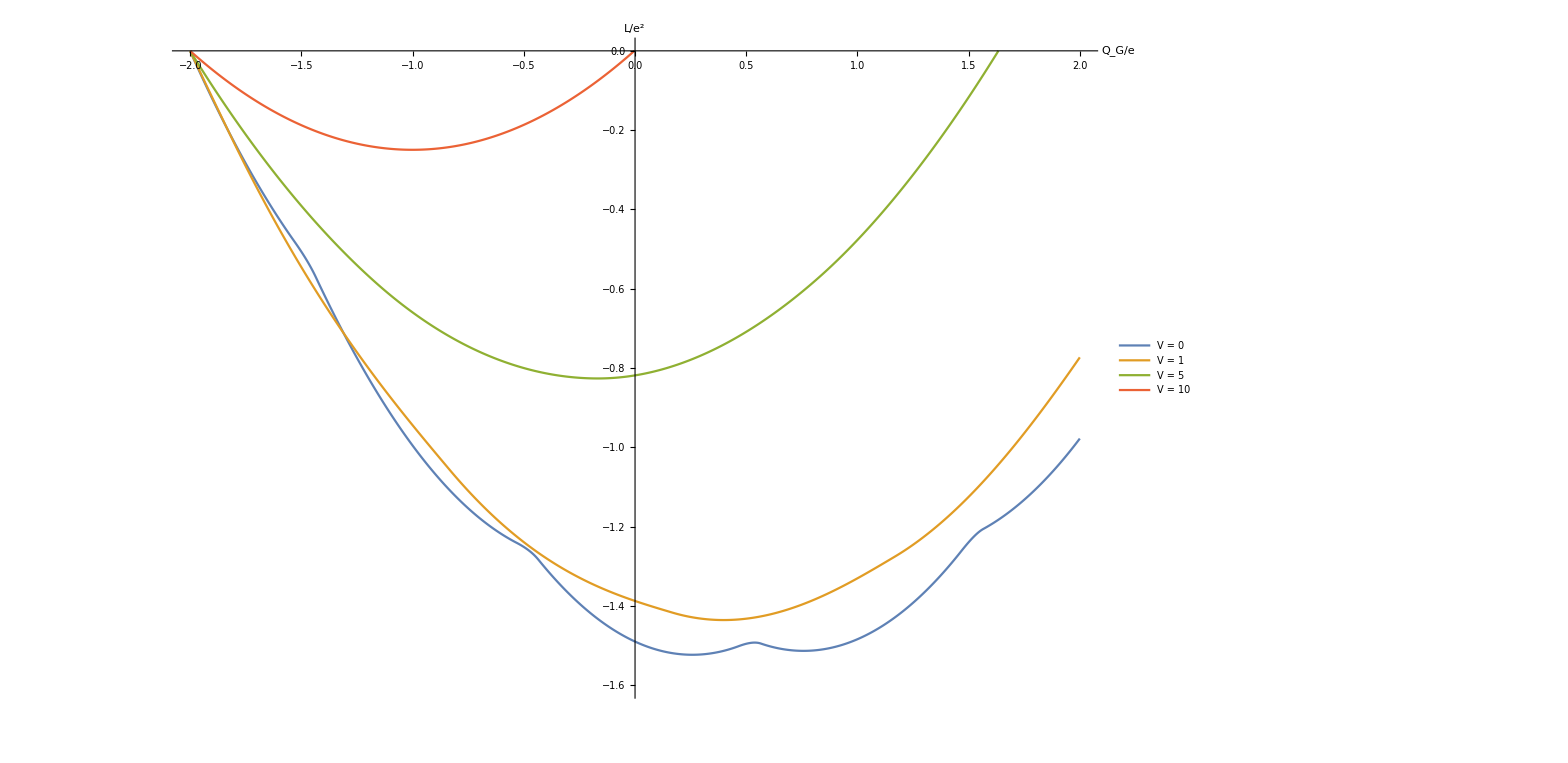

```mathematica
Qn=CG/(C1+C2+CG)((C1+C2)ϕ-C1 VL-C2 VR-navg e);

lyapunov[Vext_,Cratio_,Rratio_]:=Accumulate[Table[(Q-(Qn/.valsslow/.{x-> Vext, y-> Cratio,z-> Rratio,q-> Q}))*0.001,{Q,-2,2,0.001}]];
xvals=Table[Q,{Q,-2,2,0.001}];
ListLinePlot[{Transpose[{xvals,lyapunov[0.1,2,2]}],Transpose[{xvals,lyapunov[1,2,2]}],Transpose[{xvals,lyapunov[5,2,2]}],Transpose[{xvals,lyapunov[10,2,2]}]},AxesLabel->{"Q_G/e","L/e^2"},PlotLegends-> Placed[{"V = 0","V = 1","V = 5","V = 10"},{0.15,0.25}],BaseStyle->FontSize-> 30, PlotRange-> {{-2,2},{-1.6,0}}]
```

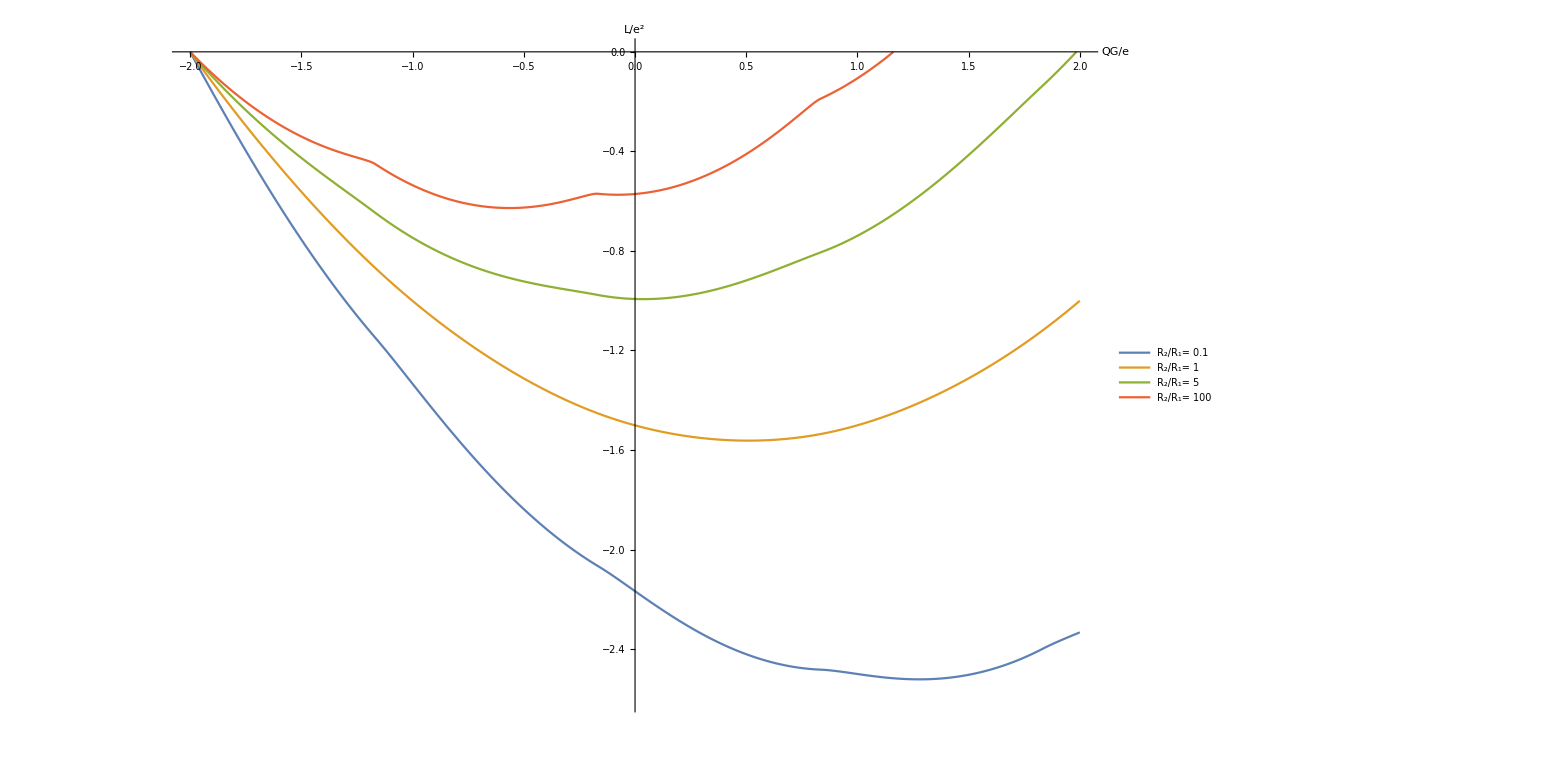

```mathematica
ListLinePlot[{Transpose[{xvals,lyapunov[2,2,0.1]}],Transpose[{xvals,lyapunov[2,2,1]}],Transpose[{xvals,lyapunov[2,2,5]}],Transpose[{xvals,lyapunov[2,2,100]}]},AxesLabel->{"QG/e","L/e^2"},PlotLegends-> Placed[{"R_2/R_1= 0.1","R_2/R_1= 1","R_2/R_1= 5","R_2/R_1= 100"},{0.15,0.25}],BaseStyle->FontSize-> 30, PlotRange-> {{-2,2},{-2.6,0}}]
```

```mathematica
line=VR+e/(2(C1+C2));
Manipulate[Plot[{U/.valsslow/.{x-> Vext,y-> Cratio,z-> Rratio , q-> gateCharge}, Ufromgate/.valsslow/.{x-> Vext,y-> Cratio,z-> Rratio , q-> gateCharge}},{gateCharge,-5,5}],{Vext,0,10},{Cratio,0.1,10},{Rratio,0.1,10}]
```

```mathematica
σ=(R2(C2 V-QG-e/2))/((QG+e/2)(R1-R2)+V(C1 R1+C2 R2));
Uapprox=(σ e +QG+VL C1+VR C2)/(C1+C2);
QGsol=Simplify[Solve[D[Uapprox,QG] == -1/CG,QG]][[1]]
```

{QG→-1/(2 (C1+C2+CG) (R1-R2)^2)(CG e R1^2-2 CG e R1 R2+CG e R2^2+2 C1^2 R1 (R1-R2) V+2 C2^2 (R1-R2) R2 V+2 √((C1+C2) CG (C1+C2+CG) e R1 (R1-R2)^2 R2 V)+C2 (R1-R2) (e R1-e R2+2 CG R2 V)+C1 (R1-R2) (e (R1-R2)+2 (CG R1+C2 (R1+R2)) V))}

```mathematica
Simplify[Solve[(QG/.QGsol)-(QG/.QGsol/.V-> V-Vp)==C2 Vp,Vp]]
```

{{Vp→0},{Vp→(CG e R2 (-R1+R2)-2 √((C1+C2) CG (C1+C2+CG) e R1 (R1-R2)^2 R2 V))/((C1+C2) (C1+C2+CG) R1 (R1-R2))}}

(-e R1-e R2+2 C1 R1 VL-2 C1 R2 VL+2 C2 R1 VR-2 C2 R2 VR)/(2 (C1+C2) (R1-R2))+((-C1 e R1 R2-C2 e R1 R2-2 CG e R1 R2) √V)/(√((C1+C2) CG (C1+C2+CG) e R1 (R1-R2)^2 R2))+((-C1 R1-C2 R2) V)/((C1+C2) (R1-R2))+O[V]^2

## Dynamics Slow Relaxation

```mathematica
RG=1000;
τ=1;
dQ[Q_]:=-Re[(Q-(Qn/.valsslow/.{x-> 2, y-> 2,z->100,q-> Q}))/(τ/.valsslow/.{x-> 2, y-> 2,z->100,q-> Q})];
s1=NDSolve[{Q'[t]==dQ[Q[t]],Q[0]==-0.16},Q,{t,0,10}];
s2=NDSolve[{Q'[t]==dQ[Q[t]],Q[0]==-0.18},Q,{t,0,10}];
```

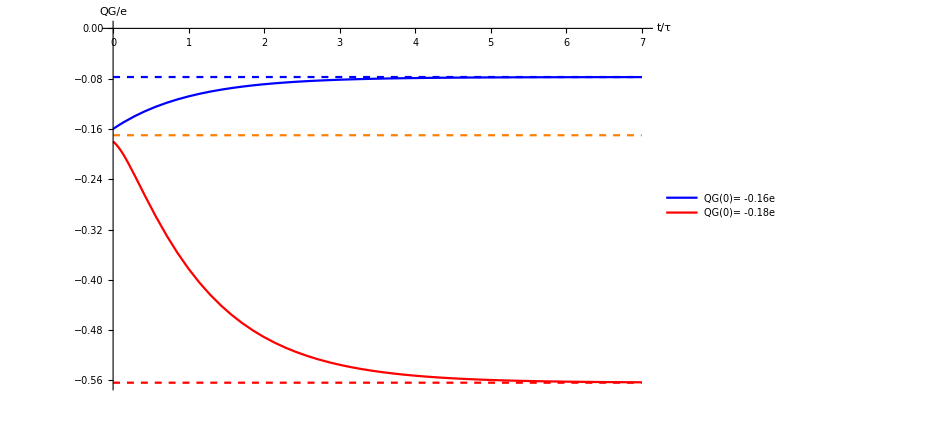

```mathematica
Plot[{Evaluate[Q[t]/.s1],Evaluate[Q[t]/.s2],-0.56373,-0.0774,-0.17},{t,0,7},AxesLabel->{"t/τ","QG/e"},PlotLegends-> Placed[{"QG(0)= -0.16e","QG(0)= -0.18e"},{0.5,0.5}],BaseStyle->FontSize-> 30, PlotStyle->{{Blue},{Red},{Red,Dashed},{Blue,Dashed},{Orange,Dashed}}]
```

```mathematica
Evaluate[Q[10]/.s2]
```

{-0.56373}

```mathematica
dQ[Q_]:=-Re[(Q-(Qn/.valsslow/.{x-> 0.01, y-> 2,z->2,q-> Q}))/(τ/.valsslow/.{x-> 0.01, y-> 2,z->2,q-> Q})];
s3=NDSolve[{Q'[t]==dQ[Q[t]],Q[0]==0.45},Q,{t,0,10}];
s4=NDSolve[{Q'[t]==dQ[Q[t]],Q[0]==0.55},Q,{t,0,10}];
```

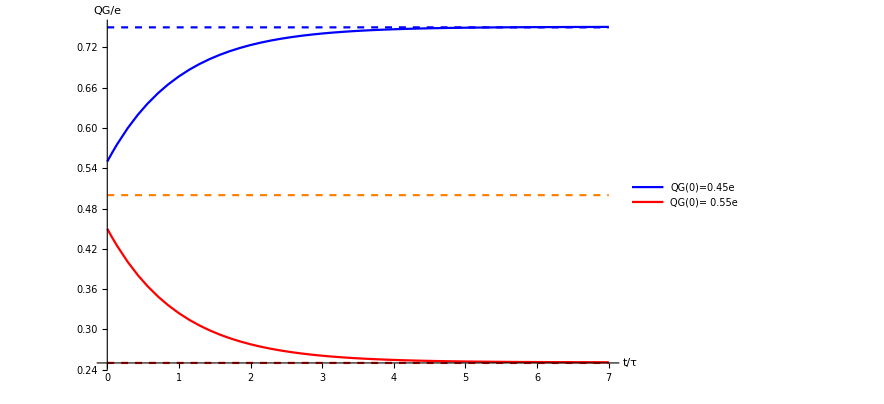

```mathematica
Plot[{Evaluate[Q[t]/.s4],Evaluate[Q[t]/.s3],0.25,0.75,0.5},{t,0,7},AxesLabel->{"t/τ","QG/e"},PlotLegends-> Placed[{"QG(0)=0.45e","QG(0)= 0.55e"},{0.5,0.5}],BaseStyle->FontSize-> 30, PlotStyle->{{Blue},{Red},{Red,Dashed},{Blue,Dashed},{Orange,Dashed}}]
```

```mathematica
Evaluate[Q[10]/.s4]
```

{0.750824}

```mathematica
Uapprox=1/(C1+C2)( (navgsmallv/.{α-> αvalslow/.V-> VL-VR, β-> βvalslow/.V-> VL-VR})  e+QG + C1 VL+ C2 VR);

QGsol = Simplify[Solve[D[Uapprox,QG]==-1/CG,QG]];
Usol = Simplify[Uapprox/.QGsol];
Ugap=Simplify[Usol[[2]] - Usmallv/.{QG-> (C2 (VL - VR) -e/2), nmin-> 1, nmax->1, V-> VL-VR}]
(-C1 V -e/2)/.valsslow/.{x-> 0.5,y-> 10, z-> 0.1}
Plot[{Uapprox/.valsslow/.{x-> 0.5,y-> 10, z-> 0.1},Usmallv/.valsslow/.{x-> 0.5,y-> 10, z-> 0.1}},{q,-1,1},Epilog->{Point/@{{QG/.QGsol[[2]]/.valsslow/.{x-> 0.5,y-> 10, z-> 0.1},Usol[[2]]/.valsslow/.{x-> 0.5,y-> 10, z-> 0.1}}}}]
```

(2 C1^2 e R1 (R1-R2) R2 (VL-VR)+2 C2^2 e R1 (R1-R2) R2 (VL-VR)+4 C2 CG e R1 (R1-R2) R2 (VL-VR)-2 e R1 √((C1+C2) CG (C1+C2+CG) e R1 (R1-R2)^2 R2 (VL-VR))-C2 √((C1+C2) CG (C1+C2+CG) e R1 (R1-R2)^2 R2 (VL-VR)) (R1 (VL-3 VR)+R2 (VL+VR))+C1 (4 C2 e R1 (R1-R2) R2 (VL-VR)+4 CG e R1 (R1-R2) R2 (VL-VR)-√((C1+C2) CG (C1+C2+CG) e R1 (R1-R2)^2 R2 (VL-VR)) (R1 (VL-3 VR)+R2 (VL+VR))))/(2 (C1+C2) (R1-R2) √((C1+C2) CG (C1+C2+CG) e R1 (R1-R2)^2 R2 (VL-VR)))

-0.545455

-Graphics-

```mathematica
δQG = Simplify[D[QG/.QGsol,V]][[1]]
δU = Simplify[D[Usol,V]][[1]]
```

-(2 C1^2 R1+2 C2^2 R2+2 C2 CG R2+2 C1 (CG R1+C2 (R1+R2))+(√((C1+C2) CG (C1+C2+CG) e R1 (R1-R2)^2 R2 V))/(R1 V-R2 V))/(2 (C1+C2+CG) (R1-R2))

(-2 CG e R1^2 R2+2 CG e R1 R2^2+C1 e R1 R2 (-R1+R2)+C2 e R1 R2 (-R1+R2)-R1 √((C1+C2) CG (C1+C2+CG) e R1 (R1-R2)^2 R2 V)-R2 √((C1+C2) CG (C1+C2+CG) e R1 (R1-R2)^2 R2 V))/(2 (R1-R2) √((C1+C2) CG (C1+C2+CG) e R1 (R1-R2)^2 R2 V))

```mathematica
Clear[ΔV]
ΔVsol = Simplify[Solve[δU ΔV+δQG/CG ΔV==Usol[[1]]- ϕ+(QG/.QGsol[[1]])/CG,ΔV]]
```

{{ΔV→(CG e (R1+R2) √((C1+C2) CG (C1+C2+CG) e R1 (R1-R2)^2 R2 V)+2 C2^2 R2 V (2 CG e R1 (R1-R2)+√((C1+C2) CG (C1+C2+CG) e R1 (R1-R2)^2 R2 V))+2 C1^2 R1 V (2 CG e (R1-R2) R2+√((C1+C2) CG (C1+C2+CG) e R1 (R1-R2)^2 R2 V))+C2 (4 CG^2 e R1 (R1-R2) R2 V+e (R1-R2) √((C1+C2) CG (C1+C2+CG) e R1 (R1-R2)^2 R2 V)+CG √((C1+C2) CG (C1+C2+CG) e R1 (R1-R2)^2 R2 V) (R2 (V-2 ϕ)+R1 (V+2 ϕ)))+C1 (4 CG^2 e R1 (R1-R2) R2 V+e (R1-R2) √((C1+C2) CG (C1+C2+CG) e R1 (R1-R2)^2 R2 V)+2 C2 V (4 CG e R1 (R1-R2) R2+(R1+R2) √((C1+C2) CG (C1+C2+CG) e R1 (R1-R2)^2 R2 V))+CG √((C1+C2) CG (C1+C2+CG) e R1 (R1-R2)^2 R2 V) (R2 (V-2 ϕ)+R1 (V+2 ϕ))))/((C1+C2) (2 C2 R2 (CG e R1 (R1-R2)+√((C1+C2) CG (C1+C2+CG) e R1 (R1-R2)^2 R2 V))+2 C1 R1 (CG e (R1-R2) R2+√((C1+C2) CG (C1+C2+CG) e R1 (R1-R2)^2 R2 V))+CG (2 CG e R1 (R1-R2) R2+(R1+R2) √((C1+C2) CG (C1+C2+CG) e R1 (R1-R2)^2 R2 V))))}}

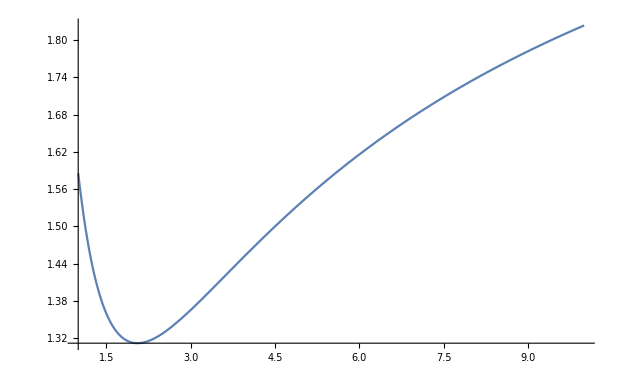

```mathematica
Plot[ΔV/.ΔVsol/.valsslow/.{y-> 2,x->3},{z,1,10}]
```

```mathematica
A=√((C1+C2) CG (C1+C2+CG) e R1 (R1-R2)^2 R2 V);
ΔVtry=Simplify[(CG e (R1+R2) +(C1+C2) (e (R1-R2) +2V(C2 R2+C1 R1)+CG  (R2 (V-2 ϕ)+R1 (V+2 ϕ)))+4 A/(R1-R2) )/(2 A/((R1-R2)V)+(C1+C2) (2 C2 R2 +2 C1 R1 +CG (R1+R2)))];
(CG e/2  -(C1+C2) e/2 ) /((C1+C2) ( C2  +CG/2 ))
```

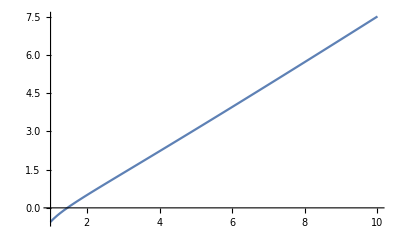

```mathematica
Plot[ΔVtry/.valsslow/.{y-> 2,z->3},{x,1,10}]
```

```mathematica
Solve[D[(e^2CG)/((C1+C2+CG)(C1+C2)(R1+R2)(CG/2(R2-R1)/(R2+R1)+C2)),CG]==0,CG]
```

{{CG→-(2 ⅈ √C2 √(C1+C2) √(R1+R2))/(√(2 R1-2 R2))},{CG→(2 ⅈ √C2 √(C1+C2) √(R1+R2))/(√(2 R1-2 R2))}}

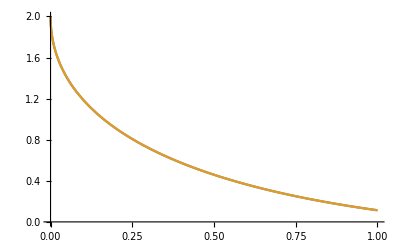

```mathematica
Ugap1=(R2 e/(C1+C2)+R1 V)/(R2-R1) -(C1+C2+2CG)√((e R1 R2  V)/(CG(C1+C2+CG)(C1+C2)(R1-R2)^2)) ;
Ugap2=(e R1 R2  V(C1+C2+2CG))/(√((C1+C2) CG (C1+C2+CG) e R1 (R1-R2)^2 R2 V))- (R2 e/(C1+C2)+R1 V)/(R1-R2) ;
Plot[{Ugap/.valsslow/.{y-> 2,z-> 2, Cs-> 3},Ugap1/.valsslow/.{y-> 2,z-> 2, Cs-> 3}},{x,0,1}]
```

```mathematica
{((e/2)/(C1+C2)(R1+R2)+R2 VL-R1 VR)/(R1-R2)-√(((C1+C2+2CG)e R1  R2 (VL-VR))/((C1+C2) CG (C1+C2+CG) (R1-R2)^2)),(2 C1^2 e R1 (R1-R2) R2 (VL-VR)+2 C2^2 e R1 (R1-R2) R2 (VL-VR)+4 C2 CG e R1 (R1-R2) R2 (VL-VR)-e (R1+R2) √((C1+C2) CG (C1+C2+CG) e R1 (R1-R2)^2 R2 (VL-VR))+2 C2 √((C1+C2) CG (C1+C2+CG) e R1 (R1-R2)^2 R2 (VL-VR)) (-R2 VL+R1 VR)+2 C1 (2 C2 e R1 (R1-R2) R2 (VL-VR)+2 CG e R1 (R1-R2) R2 (VL-VR)+√((C1+C2) CG (C1+C2+CG) e R1 (R1-R2)^2 R2 (VL-VR)) (-R2 VL+R1 VR)))/(2 (C1+C2) (R1-R2) √((C1+C2) CG (C1+C2+CG) e R1 (R1-R2)^2 R2 (VL-VR)))}
```

```mathematica
Simplify[Usmallv/.{α-> αvalslow/.V-> VL-VR, β-> βvalslow/.V-> VL-VR}/.{QG-> (C2 V -e/2)}]
```

Piecewise[{{1/2 ((e (-1+2 nmin))/(C1+C2)-V), nmax≤nmin}, {(e^2 nmin (R1-2 nmin R1+R2+2 nmin R2)-(C1+C2) V (-C1 R2 V+C2 R2 (-VL+VR)+C1 R1 (V-VL+VR))+e (C2 nmin R1 V-C1 (1+3 nmin) R2 V-C2 nmin R2 (V+2 VL-2 VR)+C2 R2 (-VL+VR)+C1 R1 (-V+3 nmin V+VL-2 nmin VL-VR+2 nmin VR)))/(2 (C1+C2) (e nmin (-R1+R2)-C1 R2 V+C2 R2 (-VL+VR)+C1 R1 (V-VL+VR))), nmax>nmin}, {0, True}}]

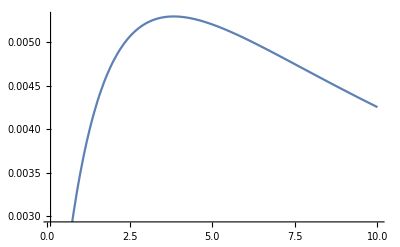

```mathematica
ΔV  = e/(CG/2(R2-R1)/(R1+R2)+C2);
ΔVupdown=ΔV CG/(R2-R1)((e R2)/(C1+C2)+R1 V - √((e R1 R2 V(C1+C2+2CG))/((C1+C2)CG(C1+C2+CG))));
ΔI = e/((C1+C2+CG)(R1+R2));
Plot[(ΔI ΔVupdown)/.{R2-> 10,R1-> 1,V-> 0,C2-> 2,C1-> 1,e-> 1},{CG,0.1,10}]
```